# Octahedron 5-Compound

### Author

Eric W. Weisstein
May 9, 2020

This notebook downloaded from http://mathworld.wolfram.com/notebooks/Polyhedra/Octahedron5-Compound.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/Octahedron5-Compound.html.

©2020 Wolfram Research, Inc. except for portions noted otherwise

## Graphic

```mathematica
PolyhedronData/@{"OctahedronFiveCompound",{"IcosahedronStellation",3}}
```

{-Graphics3D-,-Graphics3D-}

## Properties: "OctahedronFiveCompound"

```mathematica
p=PolyhedronData["OctahedronFiveCompound","Polyhedron"]
```

Polyhedron[…]

### Classes

```mathematica
PolyhedronData["OctahedronFiveCompound","Classes"]
```

{Amphichiral,Compound,Concave,Equilateral,Rigid}

### Circumsphere

```mathematica
PolyhedronData["OctahedronFiveCompound","Circumsphere"]
```

Sphere[{0,0,0},1/(√2)]

```mathematica
Norm/@PolyhedronData["OctahedronFiveCompound","VertexCoordinates"]//FullSimplify//Union
```

{1/(√2)}

### Convex

```mathematica
ConvexPolyhedronQ[p]
```

False

```mathematica
PolyhedronData["OctahedronFiveCompound","Convex"]
```

False

### EdgeCount

```mathematica
PolyhedronData["OctahedronFiveCompound","Edges"]//Length
```

60

### FaceCount

```mathematica
PolyhedronData["OctahedronFiveCompound","FaceIndices"]//Length
```

40

### GeneralizedDiameter

```mathematica
PolyhedronData["OctahedronFiveCompound","GeneralizedDiameter"]
```

√2

```mathematica
GeneralizedDiameter[p]//FullSimplify//Quiet
```

√2

### Hull

```mathematica
Max[Norm/@PolyhedronData["OctahedronFiveCompound","VertexCoordinates"]]/Max[Norm/@PolyhedronData[{"IcosahedronStellation",3},"VertexCoordinates"]]//FullSimplify//Quiet
```

2/(5+√5)

```mathematica
PolyhedronData["OctahedronFiveCompound","Hull",#]&/@{"Name","Scale"}
```

{{IcosahedronStellation,3},2/(5+√5)}

```mathematica
With[{p="OctahedronFiveCompound"},{
Graphics3D[{Red,PolyhedronData[p,"Polyhedron"]},Axes->True],
Graphics3D[{Green,PolyhedronData[p,"Hull","Polyhedron"]},Axes->True]
}]
```

{-Graphics3D-,-Graphics3D-}

```mathematica
Show[%]
```

-Graphics3D-

### Oriented

```mathematica
Graphics3D[{FaceForm[Green,Red],p}]
```

-Graphics3D-

### Polyhedra

```mathematica
Graphics3D/@PolyhedronData["OctahedronFiveCompound","Polyhedra"]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

### Simple

```mathematica
SimplePolyhedronQ[p]
```

False

### Skeleton

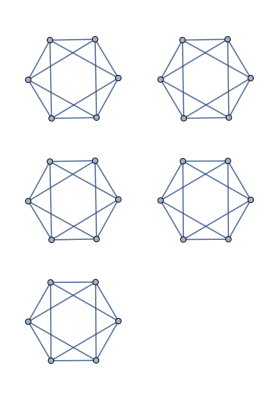

```mathematica
g=PolyhedronData["OctahedronFiveCompound","Skeleton"]
```

```mathematica
r=RecognizeGraph[g]
```

Reading CanonicalForms from raw GraphData file cache (first time only)...

Reading GraphData standard names from raw GraphData file cache (first time only)...

Building default Association of length 10369...

{}

### SurfaceArea

```mathematica
PolyhedronData["OctahedronFiveCompound","SurfaceArea"]
```

10 √3

```mathematica
N[%]
```

17.3205

```mathematica
Total[SurfaceArea/@PolyhedronData["OctahedronFiveCompound","Polyhedra"]]//N
```

17.3205

```mathematica
PolyhedronSurfaceArea[p]//N
```

17.3205

### VertexCount

```mathematica
PolyhedronData["OctahedronFiveCompound","Vertices"]//Length
```

30

### VertexSubsetHulls

```mathematica
VertexSubsetHulls[p,"Platonic"]
```

Finding equilateral triangles...

Finding potential tetrahedra from equilateral triangles...

Finding tetrahedra from potential candidates...

Finding cubes from tetrahedra...

Finding dodecahedron from cubes...

Finding octahedra by building up from equilateral triangles...

Finding dodecahedra from octahedra...

SKIPPING building up icosahedra from equilateral triangles...

{Octahedron→{{1,2,11,14,17,24},{3,5,20,23,28,30},{4,6,21,22,27,29},{7,9,13,16,18,26},{8,10,12,15,19,25}},Icosidodecahedron→{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}}}

### Volume

```mathematica
PolyhedronData["OctahedronFiveCompound","Volume"]
```

(5 √2)/3

```mathematica
Total[Volume/@PolyhedronData["OctahedronFiveCompound","Polyhedra"]]//FullSimplify
```

(5 √2)/3

```mathematica
N[%]
```

2.35702

```mathematica
Total[PolyhedronVolume/@PolyhedronData["OctahedronFiveCompound","Polyhedra"]]//N
```

2.35702

## Properties: {"IcosahedronStellation", 3}

```mathematica
p=PolyhedronData[{"IcosahedronStellation",3},"Polyhedron"]
```

Polyhedron[…]

### Centroid

```mathematica
PolyhedronData[{"IcosahedronStellation",3},"Centroid"]
```

{0,0,0}

```mathematica
RegionCentroid[p]/PolyhedronData[{"IcosahedronStellation",3},"Volume"]//N
```

{-3.55271×10^-19,3.66374×10^-19,1.77636×10^-18}

```mathematica
PolyhedronCentroid[p,PolyhedronData[{"IcosahedronStellation",3},"Volume"]]
```

{0,0,0}

### Circumsphere

```mathematica
PolyhedronData[{"IcosahedronStellation",3},"Circumsphere"]
```

Missing[NotApplicable]

```mathematica
Norm/@PolyhedronData[{"IcosahedronStellation",3},"VertexCoordinates"]//FullSimplify//Union
```

{1/2 √(25-5 √5),1/2 √(3 (3+√5)),1/2 √(5 (3+√5)),5/(√(5+√5))}

### DihedralAngles

```mathematica
Tally[PolyhedronData[{"IcosahedronStellation",3},"DihedralAngles"]]
```

{{ArcSec[-3],180}}

```mathematica
di=SimplifyNumericallyDistinct[DihedralAngles[p],"Simplification"->RootReduce,Debug->True]//Union
```

Found 1 numerically distinct expressions out of 180 total

Byte counts: {48128}

Simplifying expression 1/1 with ByteCount 48128 using RootReduce and TimeConstraint→∞

Simplified to ArcCos[-1/3] with ByteCount 104 after 0 seconds

List of simplified expressions: {ArcCos[-1/3]}

MaxMemoryUsed = 0.859087 GB

Post-simplification byte counts: {104}

{ArcCos[-1/3]}

### EdgeLengths

```mathematica
PolyhedronData[{"IcosahedronStellation",3},"EdgeLengths"]
```

{1,-1+√5,1/2 (5-√5)}

### InertiaTensor

```mathematica
PolyhedronData[{"IcosahedronStellation",3},"InertiaTensor"]
```

{{1/20 (23+5 √5),0,0},{0,1/20 (23+5 √5),0},{0,0,1/20 (23+5 √5)}}

```mathematica
N[%]
```

{{1.70902,0.,0.},{0.,1.70902,0.},{0.,0.,1.70902}}

```mathematica
MomentOfInertia[p//N,{0,0,0}]/PolyhedronData[{"IcosahedronStellation",3},"Volume"]//Chop
```

{{1.70902,0,0},{0,1.70902,0},{0,0,1.70902}}

```mathematica
PolyhedronInertiaTensor[p//N,PolyhedronData[{"IcosahedronStellation",3},"Volume"]]//Chop
```

{{1.70902,0,0},{0,1.70902,0},{0,0,1.70902}}

### Orientation

```mathematica
Graphics3D[{FaceForm[Green,Red],PolyhedronData["DodecahedronSmallTriambicIcosahedronCompoundHull","Polyhedron"]}]
```

-Graphics3D-

### SurfaceArea

```mathematica
PolyhedronData[{"IcosahedronStellation",3},"SurfaceArea"]
```

15 √(30 (3-√5))

```mathematica
N[%]
```

71.8091

```mathematica
SurfaceArea[p]//N
```

71.8091

```mathematica
SurfaceArea[p]//FullSimplify//Timing
```

$Aborted

```mathematica
PolyhedronSurfaceArea[p]//N
```

71.8091

```mathematica
PolyhedronSurfaceArea[p]//FullSimplify//Timing
```

### Volume

```mathematica
PolyhedronData[{"IcosahedronStellation",3},"Volume"]
```

25 √2

```mathematica
N[%]
```

35.3553

```mathematica
Volume[p]//N
```

35.3553

```mathematica
Volume[p]//FullSimplify//Timing
```

{3.24845,25 √2}

```mathematica
PolyhedronVolume[p]//N
```

35.3553

```mathematica
PolyhedronVolume[p]//FullSimplify//Timing
```

$Aborted

```mathematica
PolyhedronVolume[p,Method->"GaussLaw"]//N
```

35.3553

```mathematica
PolyhedronVolume[p,Method->"GaussLaw"]//FullSimplify
```

25 √2

## Interior

```mathematica
ineq=FullSimplify[PolyhedronInequalities[Flatten[Normal[PolyhedronData["Octahedron5Compound","Faces"]]],{x,y,z}]];//Timing
```

```mathematica
RegionPlot3D[And@@ineq,{x,-.5,.5},{y,-.5,.5},{z,-.5,.5},Mesh->False]
```

-Graphics3D-

```mathematica
Show[{
Graphics3D[{Opacity[.2],EdgeForm[Thickness[.001]],PolyhedronData["Octahedron5Compound","Faces"]}],RegionPlot3D[And@@ineq,{x,-.5,.5},{y,-.5,.5},{z,-.5,.5},Mesh->False]
}]
```

-Graphics3D-

```mathematica
ineq
```

{5 √2+2 √(5 (5-2 √5)) x+10 y+2 √(5 (5+2 √5)) z≥0,2 √(5 (5-2 √5)) z≤5 √2+2 √(5 (5+2 √5)) x+10 y,2 √(5 (5+2 √5)) x≤5 √2+10 y+2 √(5 (5-2 √5)) z,√2 (-5+√(50-20 √5) x+√(50+20 √5) z)≤10 y,10 y≤5 √2+2 √(5 (5-2 √5)) x+2 √(5 (5+2 √5)) z,10 y+2 √(5 (5-2 √5)) z≤5 √2+2 √(5 (5+2 √5)) x,2 √(5 (5+2 √5)) x+10 y≤5 √2+2 √(5 (5-2 √5)) z,2 (√(5 (5-2 √5)) x+5 y+√(5 (5+2 √5)) z)≤5 √2,5 √2+√(50-10 √5) x+5 (1+√5) y+2 √(5 (5-2 √5)) z≥0,2 √(5 (5+2 √5)) x≤5 √2+10 y+2 √(5 (5-2 √5)) z,5 √2+2 √(50-10 √5) x+2 √(5 (5+2 √5)) z≥0,√5 (√(50+22 √5) x+10 y)≤10 √2+√(50-10 √5) x+10 y+4 √(5 (5+2 √5)) z,5 (1+√5) y≤5 √2+√(50-10 √5) x+2 √(5 (5-2 √5)) z,2 √(5 (5+2 √5)) x+10 y≤5 √2+2 √(5 (5-2 √5)) z,5 √2+2 √(50-10 √5) x+2 √(5 (5+2 √5)) z≥0,√(10 (5+√5)) x≤5 √2+5 (-1+√5) y+2 √(5 (5+2 √5)) z,2 √(125+55 √5) z≤5+5 √5+2 √(50+20 √5) x+10 √2 y,4 √(5 (5+√5)) x+2 √(125+55 √5) z≤5 (1+√5),10 √2 y+2 √(125+55 √5) z≤5+5 √5+2 √(50+20 √5) x,4 √(5 (5+√5)) x+2 √(125+55 √5) z≤5 (1+√5),2 √(5 (5+√5)) x+√(50-20 √5) z≤5,√(50-10 √5) x+2 √(5 (5-2 √5)) z≤5 (√2+y+√5 y),2 (√(5 (5-2 √5)) x+5 y+√(5 (5+2 √5)) z)≤5 √2,2 √(5 (5+2 √5)) z≤5 √2+√(10 (5+√5)) x+5 (-1+√5) y,2 √(5 (5+√5)) x+√(50-20 √5) z≤5,√(50-10 √5) x+5 (1+√5) y+2 √(5 (5-2 √5)) z≤5 √2,2 (√(5 (5-2 √5)) x+√(5 (5+2 √5)) z)≤5 (√2+2 y),√5 (5 y+2 √(5+2 √5) z)≤√(10 (5+√5)) x+5 (√2+y),√(10 (5+√5)) x+5 (-1+√5) y≤5 √2+2 √(5 (5+2 √5)) z,5 √2+2 √(5 (5-2 √5)) x+10 y+2 √(5 (5+2 √5)) z≥0,√(10 (5+√5)) x≤5 √2+5 (-1+√5) y+2 √(5 (5+2 √5)) z,10 y≤5 √2+2 √(5 (5-2 √5)) x+2 √(5 (5+2 √5)) z,5 √2+√(50-10 √5) x+5 (1+√5) y+2 √(5 (5-2 √5)) z≥0,5+2 √(5 (5+√5)) x+√(50-20 √5) z≥0,5 (1+√5) y≤5 √2+√(50-10 √5) x+2 √(5 (5-2 √5)) z,5+2 √(5 (5+√5)) x+√(50-20 √5) z≥0,20 √(3+√5) y+√(850+220 √5) z≤10 (1+√5)+4 √(125+55 √5) x+5 √(10+4 √5) z,√(850+220 √5) z≤4 √(125+55 √5) x+5 (2+2 √5+4 √(3+√5) y+√(10+4 √5) z),√(125+55 √5) x+2 √(25-5 √5) z≤√(25-5 √5) x+5 (1+√5+√2 (3+√5) y),2 √(5 (5+√5)) x+5 √2 (3+√5) y+2 √(25-5 √5) z≤5+5 √5}

```mathematica
(int=PolyhedronFromInequalities[ineq,{x,y,z}]);//Timing
```

$Aborted

```mathematica
(int=PolyhedronFromInequalities[ineq,{x,y,z}]);//Timing
```

Simplify::time: Time spent on a transformation exceeded 300 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify will be suppressed during this calculation.

$Aborted

## Net

```mathematica
<<ExtraPackages`UnfoldPolytope`
```

```mathematica
UnfoldPolytope[Flatten[Normal[PolyhedronData[{"OctahedronFiveCompound","Split"},"Faces"]]]]
```

-Graphics3D-

## Properties

```mathematica
PolyhedronData["Octahedron","Orientations"]
```

{C2,C3,C4,C4x}

### Edge Lengths

```mathematica
poly//N//Length
```

280

```mathematica
Union[poly//N]//Length
```

240

```mathematica
PolyhedronEdges[poly//N]//Length
```

210

```mathematica
e=Together//@Union[FullSimplify[Union[PolyhedronEdgeLengths[poly]]]]
```

{2 √(1/5 (7-3 √5)),√(1/5 (3-√5)),√(7-3 √5),3-√5}

```mathematica
Sort[{2 √(1/5 (7-3 √5)),√(1/5 (3-√5)),√(7-3 √5),3-√5},Less]
```

{√(1/5 (3-√5)),2 √(1/5 (7-3 √5)),√(7-3 √5),3-√5}

```mathematica
N[{√(1/5 (3-√5)),2 √(1/5 (7-3 √5)),√(7-3 √5),3-√5}]
```

{0.390879,0.483153,0.540182,0.763932}

```mathematica
{0.3908790151697096,0.4831530337279323,0.5401815134754526,0.7639320225002102}/0.3908790151697096
```

{1.,1.23607,1.38197,1.9544}

```mathematica
{2,2.5,2.8}/2
```

{1,1.25,1.4}

### InertiaTensor

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

Get::noopen: Cannot open "Utilities`FilterOptions`".

Needs::nocont: Context "Utilities`FilterOptions`" was not created when Needs was evaluated.

Get::noopen: Cannot open "NumberTheory`Recognize`".

Needs::nocont: Context "NumberTheory`Recognize`" was not created when Needs was evaluated.

SetDelayed::write: Tag Ellipsoid in Ellipsoid[a_, b_, c_] is Protected.

SetDelayed::write: Tag Pivot in Pivot[d_ ? MatrixQ, bv_ ? VectorQ, nbv_ ? VectorQ, i_Integer, j_Integer, m_Integer, n_Integer] is Protected.

SetDelayed::write: Tag Pivot in Pivot[d_ ? MatrixQ, bv_ ? VectorQ, nbv_ ? VectorQ, i_Integer, j_Integer] is Protected.

General::stop: Further output of SetDelayed :: write will be suppressed during this calculation.

```mathematica
?Inertia*
```

InertiaTensor[gc, simp1, simp2] computes the moment of inertia tensor of the specified GraphicsComplex-specified polyhedron using Gauss's law.  InertiaTensor[gc, vol, simp1, simp2] uses the precomputed volume and applies simplification functions 1 and 2 at approriate steps.  InertiaTensot[ent, simp1, simp2] computes the moment of inertia tensor of the specified PolyhedronData object using the given simplification functions.

#### Intersecting

```mathematica
(#->PolyhedronData[{"Octahedron",#},"InertiaTensor"])&/@PolyhedronData["Octahedron","Orientations"]//Column
```

C2→{{1/10,0,0},{0,1/10,0},{0,0,1/10}}
C3→{{1/10,0,0},{0,1/10,0},{0,0,1/10}}
C4→{{1/10,0,0},{0,1/10,0},{0,0,1/10}}
C4x→{{1/10,0,0},{0,1/10,0},{0,0,1/10}}

```mathematica
InertiaTensor[PolyhedronData[{"OctahedronFiveCompound","Intersecting"},"Faces"]]//FullSimplify//Timing
```

{67.53707,{{1/10,0,0},{0,1/10,0},{0,0,1/10}}}

#### Split

```mathematica
InertiaTensor[PolyhedronData[{"OctahedronFiveCompound","Split"},"Faces"]]//FullSimplify//Timing
```

{194.46344,{{1/20 (23+5 √5),0,0},{0,1/20 (23+5 √5),0},{0,0,1/20 (23+5 √5)}}}

### SurfaceArea

#### Intersecting

```mathematica
PolyhedronData[{"OctahedronFiveCompound","Intersecting"},"SurfaceArea"]
```

10 √3

```mathematica
RootReduce[PolyhedronSurfaceArea[PolyhedronData[{"OctahedronFiveCompound","Intersecting"},"Faces"]]]//FullSimplify//Timing
```

{12.9468,10 √3}

#### Split

```mathematica
PolyhedronData[{"OctahedronFiveCompound","Split"},"SurfaceArea"]
```

15 √(30 (3-√5))

```mathematica
PolyhedronData[{"OctahedronFiveCompound","Split"},"SurfaceArea"]//FullSimplify
```

-15 √3 (-5+√5)

```mathematica
RootReduce[PolyhedronSurfaceArea[PolyhedronData[{"OctahedronFiveCompound","Split"},"Faces"]]]//FullSimplify//Timing
```

{19.0288,-15 √3 (-5+√5)}

### Volume

#### Intersecting

```mathematica
Graphics3D[{FaceForm[Blue,Red],Normal@PolyhedronData[{"OctahedronFiveCompound","Intersecting"},"Faces"]},Boxed->False,Method->{"ShrinkWrap"->True},ImageSize->Small]
```

-Graphics3D-

```mathematica
PolyhedronData[{"OctahedronFiveCompound","Intersecting"},"Volume"]
```

(5 √2)/3

```mathematica
RootReduce[MyVolume[PolyhedronData[{"OctahedronFiveCompound","Intersecting"},"Faces"]]]//FullSimplify//Timing
```

{1.49529,(5 √2)/3}

```mathematica
RootReduce[PolyhedronVolume[PolyhedronData[{"OctahedronFiveCompound","Intersecting"},"Faces"]]]//FullSimplify//Timing
```

{570.151,(5 √2)/3}

```mathematica
PolyhedronData[{"OctahedronFiveCompound","Intersecting"},"RegionFunction"]
```

Missing[NotAvailable]

#### Split

```mathematica
Graphics3D[{FaceForm[Blue,Red],Normal@PolyhedronData[{"OctahedronFiveCompound","Split"},"Faces"]},Boxed->False,Method->{"ShrinkWrap"->True},ImageSize->Small]
```

-Graphics3D-

```mathematica
PolyhedronData[{"OctahedronFiveCompound","Split"},"Volume"]
```

25 √2

```mathematica
RootReduce[MyVolume[PolyhedronData[{"OctahedronFiveCompound","Split"},"Faces"]]]//FullSimplify//Timing
```

{5.08975,25 √2}

```mathematica
RootReduce[PolyhedronVolume[PolyhedronData[{"OctahedronFiveCompound","Split"},"Faces"]]]//FullSimplify//Timing
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating Abs[1/2 √(2 + 4 Power[« 2 »]) (5 - Power[« 2 »]) - 1/4 √(1 - Power[« 2 »]) (5 + √5) + 1/4 √(1 - Power[« 2 »]) (25/2 + 5 Power[« 2 »]) - 1/4 √(5 - Power[« 2 »]) (25/2 + 5 Power[« 2 »])].

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating Abs[1/2 - √5/4 + 1/4 √(5 + 11 Power[« 2 »]) (5 - Power[« 2 »]) - 1/8 √5 (5 - Power[« 2 »]) (5 + √5)].

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating Abs[1/4 √(5 + 11 Power[« 2 »]) (5 - Power[« 2 »]) + 1/4 √(1 - Power[« 2 »]) (5 + √5) - 1/8 √5 (1 - Power[« 2 »]) (5 + √5) - 1/8 √5 (5 - Power[« 2 »]) (5 + √5)].

General::stop: Further output of N will be suppressed during this calculation.

{1771.43,25 √2}

```mathematica
PolyhedronData[{"OctahedronFiveCompound","Split"},"RegionFunction"]
```

Missing[NotAvailable]

## Convex Hull

```mathematica
Show[GraphicsArray[HullSpiderweb[poly]],GraphicsSpacing->{-.2}]
```

⁃GraphicsArray⁃

## Construction

```mathematica
Graphics3D[{{Opacity[.05],PolyhedronData["Octahedron5Compound","Faces"]},Flatten[Normal[PolyhedronData["Octahedron5Compound","Faces"]]][[2]]}]
```

-Graphics3D-

### Intersecting via Dual

General::obspkg: Graphics`Shapes` is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

ListSurfacePlot3D::shdw: Symbol ListSurfacePlot3D appears in multiple contexts Graphics`Graphics3D`System`; definitions in context Graphics`Graphics3D` may shadow or be shadowed by other definitions.

```mathematica
Graphics3D[p=Dual/@Polyhedron[Cube5Compound]]
```

-Graphics3D-

```mathematica
Graphics3D[{{Opacity[.05],p},Flatten[p][[2]]}]
```

-Graphics3D-

### Intersecting by Hand

```mathematica
<<DiscreteMath`Combinatorica`
```

```mathematica
v=PolyhedronVertices[Icosidodecahedron];
```

```mathematica
Show[Graphics3D[{
Polyhedron[Icosidodecahedron],
PointSize[.05],Point/@v[[{18,7}]]
}],Boxed->False]
```

⁃Graphics3D⁃

```mathematica
l=RootReduce[Sqrt[#.#]&[Subtract@@v[[{7,18}]]]]
```

Root[4-6 #1^2+#1^4&,4]

```mathematica
l2=FullSimplify[l^2]
```

3+√5

```mathematica
distance[l_]:=#.#&[Subtract@@v[[l]]]
```

```mathematica
Binomial[30,2]
```

435

```mathematica
Timing[edges=Select[KSubsets[Range[30],2],Abs[distance[#]-l2]<10^-8&]]
```

General::spell1: Possible spelling error: new symbol name "edges" is similar to existing symbol "Edges".

$MaxExtraPrecision::meprec: In increasing internal precision while attempting to evaluate √Im[Root[« 1 » &, 1]^2]^2 + (« 1 »)^2, the limit $MaxExtraPrecision = 50. was reached. Increasing the value of $MaxExtraPrecision may help resolve the uncertainty.

$MaxExtraPrecision::meprec: In increasing internal precision while attempting to evaluate √(-2 + 2/√5 - √5 + 1/4\ (« 1 »)^2 + 1/10\ (5 + √5))^2, the limit $MaxExtraPrecision = 50. was reached. Increasing the value of $MaxExtraPrecision may help resolve the uncertainty.

$MaxExtraPrecision::meprec: In increasing internal precision while attempting to evaluate √Im[Root[« 1 » &, 1]^2]^2 + (« 1 »)^2, the limit $MaxExtraPrecision = 50. was reached. Increasing the value of $MaxExtraPrecision may help resolve the uncertainty.

General::stop: Further output of $MaxExtraPrecision :: "meprec" will be suppressed during this calculation.

{0.54 Second,{{1,11},{1,14},{1,17},{1,24},{2,11},{2,14},{2,17},{2,24},{3,5},{3,20},{3,23},{3,28},{4,6},{4,21},{4,22},{4,27},{5,20},{5,23},{5,30},{6,21},{6,22},{6,29},{7,9},{7,16},{7,18},{7,26},{8,10},{8,15},{8,19},{8,25},{9,13},{9,16},{9,18},{10,12},{10,15},{10,19},{11,17},{11,24},{12,15},{12,19},{12,25},{13,16},{13,18},{13,26},{14,17},{14,24},{15,25},{16,26},{18,26},{19,25},{20,28},{20,30},{21,27},{21,29},{22,27},{22,29},{23,28},{23,30},{27,29},{28,30}}}

```mathematica
Length[edges]
```

60

```mathematica
Intersection@@{{1,11},{1,14}}
```

{1}

```mathematica
Complement[Flatten[{{1,11},{1,14}}],{1}]
```

{11,14}

```mathematica
MemberQ[edges,{11,17}]
```

True

```mathematica
triangles=Union[Union[Flatten[#]]&/@Select[KSubsets[edges,2],(i=Intersection@@#)≠{}&&MemberQ[edges,Sort[Complement[Flatten[#],i]]]&]]
```

{{1,11,17},{1,11,24},{1,14,17},{1,14,24},{2,11,17},{2,11,24},{2,14,17},{2,14,24},{3,5,20},{3,5,23},{3,20,28},{3,23,28},{4,6,21},{4,6,22},{4,21,27},{4,22,27},{5,20,30},{5,23,30},{6,21,29},{6,22,29},{7,9,16},{7,9,18},{7,16,26},{7,18,26},{8,10,15},{8,10,19},{8,15,25},{8,19,25},{9,13,16},{9,13,18},{10,12,15},{10,12,19},{12,15,25},{12,19,25},{13,16,26},{13,18,26},{20,28,30},{21,27,29},{22,27,29},{23,28,30}}

```mathematica
Length[triangles]
```

40

```mathematica
Show[Graphics3D[Polygon[v[[#]]]&/@triangles],Boxed->False]
```

⁃Graphics3D⁃

```mathematica
First/@OrientCentered[Polygon[v[[#]]]&/@triangles]/.Thread[v->Range[Length[v]]]
```

{{1,11,17},{24,11,1},{17,14,1},{1,14,24},{17,11,2},{2,11,24},{2,14,17},{24,14,2},{3,5,20},{23,5,3},{3,20,28},{28,23,3},{21,6,4},{4,6,22},{27,21,4},{4,22,27},{30,20,5},{5,23,30},{6,21,29},{29,22,6},{7,9,16},{18,9,7},{7,16,26},{26,18,7},{15,10,8},{8,10,19},{25,15,8},{8,19,25},{9,13,16},{18,13,9},{15,12,10},{10,12,19},{12,15,25},{25,19,12},{26,16,13},{13,18,26},{30,28,20},{21,27,29},{29,27,22},{23,28,30}}

```mathematica
SplitPolyhedron[Octahedron5Compound]:=
	Flatten[First[NonIntersectingPolygons[Graphics3D[Polyhedron[Octahedron5Compound]]]]]
```

### Split

```mathematica
v=PolyhedronData["Octahedron5Compound","VertexCoordinates"];
```

```mathematica
e=Flatten[Normal[PolyhedronData["Octahedron5Compound","Edges"]]];
```

```mathematica
e[[1]]
```

Line[{{0,-1/(√2),0},{-1/2 √(1+1/(√5)),0,-1/2 √(1-1/(√5))}}]

```mathematica
Length[e]
```

2

```mathematica
Length[pts=Union[Flatten[Intersection3D@@@Subsets[e,{2}]]]]//Quiet//Timing
```

{10.2555,390}

```mathematica
Graphics3D[{PolyhedronData["Octahedron5Compound","Faces"],PointSize[.02],Point[pts[[All,1]]]},Boxed->False]
```

-Graphics3D-

```mathematica
l=pts[[All,1]];
```

```mathematica
Export["expr.m",l]
```

expr.m

```mathematica
ByteCount[l=Get["expr.m"]]
```

26092328

```mathematica
pts2=RootReduce[l];//Timing
```

{433.342,Null}

```mathematica
Length[vs=Split[SortBy[{RootReduce[Norm[#]],#}&/@pts2,N],First[#1]==First[#2]&]]//Timing
```

{3.69563,5}

```mathematica
Length/@vs
```

{120,60,30,60,120}

```mathematica
ds=ToRadicals[#[[1,1]]&/@vs]//FullSimplify
```

{√(5/2-√5),√(3/10),1/(√2),√(3/2),√(5/2+√5)}

```mathematica
N[%]
```

{0.513743,0.547723,0.707107,1.22474,2.17625}

```mathematica
Graphics3D[{PolyhedronData["Octahedron5Compound","Faces"],PointSize[.03],
Point[vs[[1]][[All,2]]],
Red,Point[vs[[2]][[All,2]]],
Green,Point[vs[[3]][[All,2]]]
}//N,Boxed->False]
```

-Graphics3D-

```mathematica
chs=ConvexHull3D[#[[All,2]]]&/@vs;//Timing
```

{2.64407,Null}

```mathematica
chs
```

{{Polygon[{{Root[4-20 #1^2+5 #1^4&,2],0,Root[1-20 #1^2+20 #1^4&,3]},{Root[1-10 #1^2+20 #1^4&,2],Root[1-14 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,2]},{Root[1-50 #1^2+20 #1^4&,2],Root[1-6 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,3]}}],Polygon[{{Root[4-20 #1^2+5 #1^4&,2],0,Root[1-20 #1^2+20 #1^4&,3]},{Root[1-10 #1^2+20 #1^4&,2],Root[1-14 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,2]},{Root[1-10 #1^2+20 #1^4&,2],Root[1-14 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,2]}}],Polygon[{{Root[4-20 #1^2+5 #1^4&,2],0,Root[1-20 #1^2+20 #1^4&,3]},{Root[1-50 #1^2+20 #1^4&,2],Root[1-6 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,3]},{0,0,Root[5-20 #1^2+4 #1^4&,3]}}],Polygon[{{Root[4-20 #1^2+5 #1^4&,2],0,Root[1-20 #1^2+20 #1^4&,3]},{Root[1-50 #1^2+20 #1^4&,2],Root[1-6 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,3]},{Root[1-10 #1^2+20 #1^4&,2],Root[1-14 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,2]}}],Polygon[{{Root[4-20 #1^2+5 #1^4&,2],0,Root[1-20 #1^2+20 #1^4&,3]},{0,0,Root[5-20 #1^2+4 #1^4&,3]},{Root[1-50 #1^2+20 #1^4&,2],Root[1-6 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,3]}}],Polygon[{{Root[1-10 #1^2+20 #1^4&,2],Root[1-14 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,2]},{Root[1-10 #1^2+20 #1^4&,2],Root[1-14 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,2]},{0,0,Root[5-20 #1^2+4 #1^4&,2]}}],Polygon[{{Root[1-10 #1^2+20 #1^4&,2],Root[1-14 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,2]},{0,0,Root[5-20 #1^2+4 #1^4&,2]},{Root[1-50 #1^2+20 #1^4&,3],Root[1-6 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,2]}}],Polygon[{{Root[1-10 #1^2+20 #1^4&,2],Root[1-14 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,2]},{Root[1-50 #1^2+20 #1^4&,3],Root[1-6 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,2]},{Root[1-50 #1^2+20 #1^4&,2],Root[1-6 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,3]}}],Polygon[{{Root[1-10 #1^2+20 #1^4&,2],Root[1-14 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,2]},{Root[1-50 #1^2+20 #1^4&,2],Root[1-6 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,3]},{Root[1-50 #1^2+20 #1^4&,3],Root[1-6 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,2]}}],Polygon[{{Root[1-10 #1^2+20 #1^4&,2],Root[1-14 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,2]},{Root[1-50 #1^2+20 #1^4&,3],Root[1-6 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,2]},{0,0,Root[5-20 #1^2+4 #1^4&,2]}}],Polygon[{{Root[1-50 #1^2+20 #1^4&,2],Root[1-6 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,3]},{Root[1-50 #1^2+20 #1^4&,3],Root[1-6 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,2]},{Root[1-10 #1^2+20 #1^4&,3],Root[1-14 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,3]}}],Polygon[{{Root[1-50 #1^2+20 #1^4&,2],Root[1-6 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,3]},{Root[1-10 #1^2+20 #1^4&,3],Root[1-14 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,3]},{0,0,Root[5-20 #1^2+4 #1^4&,3]}}],Polygon[{{Root[1-50 #1^2+20 #1^4&,2],Root[1-6 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,3]},{0,0,Root[5-20 #1^2+4 #1^4&,3]},{Root[1-10 #1^2+20 #1^4&,3],Root[1-14 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,3]}}],Polygon[{{Root[1-50 #1^2+20 #1^4&,2],Root[1-6 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,3]},{Root[1-10 #1^2+20 #1^4&,3],Root[1-14 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,3]},{Root[1-50 #1^2+20 #1^4&,3],Root[1-6 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,2]}}],Polygon[{{0,0,Root[5-20 #1^2+4 #1^4&,2]},{Root[1-50 #1^2+20 #1^4&,3],Root[1-6 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,2]},{Root[4-20 #1^2+5 #1^4&,3],0,Root[1-20 #1^2+20 #1^4&,2]}}],Polygon[{{0,0,Root[5-20 #1^2+4 #1^4&,2]},{Root[4-20 #1^2+5 #1^4&,3],0,Root[1-20 #1^2+20 #1^4&,2]},{Root[1-50 #1^2+20 #1^4&,3],Root[1-6 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,2]}}],Polygon[{{0,0,Root[5-20 #1^2+4 #1^4&,3]},{Root[1-10 #1^2+20 #1^4&,3],Root[1-14 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,3]},{Root[1-10 #1^2+20 #1^4&,3],Root[1-14 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,3]}}],Polygon[{{Root[1-50 #1^2+20 #1^4&,3],Root[1-6 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,2]},{Root[4-20 #1^2+5 #1^4&,3],0,Root[1-20 #1^2+20 #1^4&,2]},{Root[1-10 #1^2+20 #1^4&,3],Root[1-14 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,3]}}],Polygon[{{Root[1-50 #1^2+20 #1^4&,3],Root[1-6 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,2]},{Root[1-10 #1^2+20 #1^4&,3],Root[1-14 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,3]},{Root[4-20 #1^2+5 #1^4&,3],0,Root[1-20 #1^2+20 #1^4&,2]}}],Polygon[{{Root[1-10 #1^2+20 #1^4&,3],Root[1-14 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,3]},{Root[4-20 #1^2+5 #1^4&,3],0,Root[1-20 #1^2+20 #1^4&,2]},{Root[1-10 #1^2+20 #1^4&,3],Root[1-14 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,3]}}]},{Polygon[{{Root[1-100 #1^2+500 #1^4&,1],1/(√10),Root[1-100 #1^2+500 #1^4&,3]},{Root[1-50 #1^2+500 #1^4&,1],Root[1-30 #1^2+100 #1^4&,3],Root[1-100 #1^2+500 #1^4&,4]},{Root[1-50 #1^2+500 #1^4&,1],Root[1-30 #1^2+100 #1^4&,2],Root[1-100 #1^2+500 #1^4&,4]},{Root[1-100 #1^2+500 #1^4&,1],-1/(√10),Root[1-100 #1^2+500 #1^4&,3]},{Root[4-50 #1^2+125 #1^4&,1],0,Root[1-100 #1^2+500 #1^4&,2]}}],Polygon[{{Root[1-100 #1^2+500 #1^4&,2],1/(√10),Root[1-100 #1^2+500 #1^4&,1]},{Root[1-50 #1^2+500 #1^4&,2],Root[1-30 #1^2+100 #1^4&,4],Root[1-100 #1^2+500 #1^4&,2]},{Root[1-100 #1^2+500 #1^4&,1],1/(√10),Root[1-100 #1^2+500 #1^4&,3]},{Root[4-50 #1^2+125 #1^4&,1],0,Root[1-100 #1^2+500 #1^4&,2]},{Root[4-50 #1^2+125 #1^4&,2],0,Root[1-100 #1^2+500 #1^4&,1]}}],Polygon[{{Root[1-100 #1^2+500 #1^4&,2],-1/(√10),Root[1-100 #1^2+500 #1^4&,1]},{Root[4-50 #1^2+125 #1^4&,2],0,Root[1-100 #1^2+500 #1^4&,1]},{Root[4-50 #1^2+125 #1^4&,1],0,Root[1-100 #1^2+500 #1^4&,2]},{Root[1-100 #1^2+500 #1^4&,1],-1/(√10),Root[1-100 #1^2+500 #1^4&,3]},{Root[1-50 #1^2+500 #1^4&,2],Root[1-30 #1^2+100 #1^4&,1],Root[1-100 #1^2+500 #1^4&,2]}}],Polygon[{{Root[1-50 #1^2+500 #1^4&,3],Root[1-30 #1^2+100 #1^4&,1],Root[1-100 #1^2+500 #1^4&,3]},{Root[1-100 #1^2+500 #1^4&,3],-1/(√10),Root[1-100 #1^2+500 #1^4&,4]},{Root[1-50 #1^2+500 #1^4&,1],Root[1-30 #1^2+100 #1^4&,2],Root[1-100 #1^2+500 #1^4&,4]},{Root[1-100 #1^2+500 #1^4&,1],-1/(√10),Root[1-100 #1^2+500 #1^4&,3]},{Root[1-50 #1^2+500 #1^4&,2],Root[1-30 #1^2+100 #1^4&,1],Root[1-100 #1^2+500 #1^4&,2]}}],Polygon[{{Root[1-50 #1^2+500 #1^4&,3],Root[1-30 #1^2+100 #1^4&,4],Root[1-100 #1^2+500 #1^4&,3]},{Root[1-50 #1^2+500 #1^4&,2],Root[1-30 #1^2+100 #1^4&,4],Root[1-100 #1^2+500 #1^4&,2]},{Root[1-100 #1^2+500 #1^4&,1],1/(√10),Root[1-100 #1^2+500 #1^4&,3]},{Root[1-50 #1^2+500 #1^4&,1],Root[1-30 #1^2+100 #1^4&,3],Root[1-100 #1^2+500 #1^4&,4]},{Root[1-100 #1^2+500 #1^4&,3],1/(√10),Root[1-100 #1^2+500 #1^4&,4]}}],Polygon[{{Root[1-50 #1^2+500 #1^4&,4],Root[1-30 #1^2+100 #1^4&,2],Root[1-100 #1^2+500 #1^4&,1]},{Root[1-50 #1^2+500 #1^4&,4],Root[1-30 #1^2+100 #1^4&,3],Root[1-100 #1^2+500 #1^4&,1]},{Root[1-100 #1^2+500 #1^4&,2],1/(√10),Root[1-100 #1^2+500 #1^4&,1]},{Root[4-50 #1^2+125 #1^4&,2],0,Root[1-100 #1^2+500 #1^4&,1]},{Root[1-100 #1^2+500 #1^4&,2],-1/(√10),Root[1-100 #1^2+500 #1^4&,1]}}],Polygon[{{Root[4-50 #1^2+125 #1^4&,3],0,Root[1-100 #1^2+500 #1^4&,4]},{Root[1-100 #1^2+500 #1^4&,3],1/(√10),Root[1-100 #1^2+500 #1^4&,4]},{Root[1-50 #1^2+500 #1^4&,1],Root[1-30 #1^2+100 #1^4&,3],Root[1-100 #1^2+500 #1^4&,4]},{Root[1-50 #1^2+500 #1^4&,1],Root[1-30 #1^2+100 #1^4&,2],Root[1-100 #1^2+500 #1^4&,4]},{Root[1-100 #1^2+500 #1^4&,3],-1/(√10),Root[1-100 #1^2+500 #1^4&,4]}}],Polygon[{{Root[1-100 #1^2+500 #1^4&,4],-1/(√10),Root[1-100 #1^2+500 #1^4&,2]},{Root[1-50 #1^2+500 #1^4&,4],Root[1-30 #1^2+100 #1^4&,2],Root[1-100 #1^2+500 #1^4&,1]},{Root[1-100 #1^2+500 #1^4&,2],-1/(√10),Root[1-100 #1^2+500 #1^4&,1]},{Root[1-50 #1^2+500 #1^4&,2],Root[1-30 #1^2+100 #1^4&,1],Root[1-100 #1^2+500 #1^4&,2]},{Root[1-50 #1^2+500 #1^4&,3],Root[1-30 #1^2+100 #1^4&,1],Root[1-100 #1^2+500 #1^4&,3]}}],Polygon[{{Root[1-100 #1^2+500 #1^4&,4],1/(√10),Root[1-100 #1^2+500 #1^4&,2]},{Root[1-50 #1^2+500 #1^4&,3],Root[1-30 #1^2+100 #1^4&,4],Root[1-100 #1^2+500 #1^4&,3]},{Root[1-50 #1^2+500 #1^4&,2],Root[1-30 #1^2+100 #1^4&,4],Root[1-100 #1^2+500 #1^4&,2]},{Root[1-100 #1^2+500 #1^4&,2],1/(√10),Root[1-100 #1^2+500 #1^4&,1]},{Root[1-50 #1^2+500 #1^4&,4],Root[1-30 #1^2+100 #1^4&,3],Root[1-100 #1^2+500 #1^4&,1]}}],Polygon[{{Root[4-50 #1^2+125 #1^4&,4],0,Root[1-100 #1^2+500 #1^4&,3]},{Root[4-50 #1^2+125 #1^4&,3],0,Root[1-100 #1^2+500 #1^4&,4]},{Root[1-100 #1^2+500 #1^4&,3],-1/(√10),Root[1-100 #1^2+500 #1^4&,4]},{Root[1-50 #1^2+500 #1^4&,3],Root[1-30 #1^2+100 #1^4&,1],Root[1-100 #1^2+500 #1^4&,3]},{Root[1-100 #1^2+500 #1^4&,4],-1/(√10),Root[1-100 #1^2+500 #1^4&,2]}}],Polygon[{{Root[4-50 #1^2+125 #1^4&,4],0,Root[1-100 #1^2+500 #1^4&,3]},{Root[1-100 #1^2+500 #1^4&,4],1/(√10),Root[1-100 #1^2+500 #1^4&,2]},{Root[1-50 #1^2+500 #1^4&,3],Root[1-30 #1^2+100 #1^4&,4],Root[1-100 #1^2+500 #1^4&,3]},{Root[1-100 #1^2+500 #1^4&,3],1/(√10),Root[1-100 #1^2+500 #1^4&,4]},{Root[4-50 #1^2+125 #1^4&,3],0,Root[1-100 #1^2+500 #1^4&,4]}}],Polygon[{{Root[1-100 #1^2+500 #1^4&,4],1/(√10),Root[1-100 #1^2+500 #1^4&,2]},{Root[4-50 #1^2+125 #1^4&,4],0,Root[1-100 #1^2+500 #1^4&,3]},{Root[1-100 #1^2+500 #1^4&,4],-1/(√10),Root[1-100 #1^2+500 #1^4&,2]},{Root[1-50 #1^2+500 #1^4&,4],Root[1-30 #1^2+100 #1^4&,2],Root[1-100 #1^2+500 #1^4&,1]},{Root[1-50 #1^2+500 #1^4&,4],Root[1-30 #1^2+100 #1^4&,3],Root[1-100 #1^2+500 #1^4&,1]}}]},{Polygon[{{Root[5-40 #1^2+64 #1^4&,1],Root[1-24 #1^2+64 #1^4&,2],0},{Root[5-40 #1^2+64 #1^4&,1],Root[1-24 #1^2+64 #1^4&,3],0},{Root[1-10 #1^2+20 #1^4&,1],0,Root[1-10 #1^2+20 #1^4&,2]}}],Polygon[{{Root[5-40 #1^2+64 #1^4&,1],Root[1-24 #1^2+64 #1^4&,2],0},{Root[5-40 #1^2+64 #1^4&,2],Root[1-24 #1^2+64 #1^4&,1],0},{Root[1-80 #1^2+320 #1^4&,1],-1/(2 √2),Root[1-10 #1^2+20 #1^4&,3]}}],Polygon[{{Root[5-40 #1^2+64 #1^4&,1],Root[1-24 #1^2+64 #1^4&,3],0},{Root[1-80 #1^2+320 #1^4&,1],1/(2 √2),Root[1-10 #1^2+20 #1^4&,3]},{Root[5-40 #1^2+64 #1^4&,2],Root[1-24 #1^2+64 #1^4&,4],0}}],Polygon[{{Root[1-10 #1^2+20 #1^4&,1],0,Root[1-10 #1^2+20 #1^4&,2]},{Root[1-40 #1^2+320 #1^4&,1],Root[1-24 #1^2+64 #1^4&,3],Root[1-10 #1^2+20 #1^4&,1]},{Root[1-40 #1^2+320 #1^4&,1],Root[1-24 #1^2+64 #1^4&,2],Root[1-10 #1^2+20 #1^4&,1]}}],Polygon[{{Root[1-80 #1^2+320 #1^4&,1],-1/(2 √2),Root[1-10 #1^2+20 #1^4&,3]},{Root[1-80 #1^2+320 #1^4&,2],-1/(2 √2),Root[1-10 #1^2+20 #1^4&,4]},{Root[1-10 #1^2+20 #1^4&,2],0,Root[1-10 #1^2+20 #1^4&,4]}}],Polygon[{{Root[1-80 #1^2+320 #1^4&,1],1/(2 √2),Root[1-10 #1^2+20 #1^4&,3]},{Root[1-10 #1^2+20 #1^4&,2],0,Root[1-10 #1^2+20 #1^4&,4]},{Root[1-80 #1^2+320 #1^4&,2],1/(2 √2),Root[1-10 #1^2+20 #1^4&,4]}}],Polygon[{{Root[5-40 #1^2+64 #1^4&,2],Root[1-24 #1^2+64 #1^4&,1],0},{Root[1-40 #1^2+320 #1^4&,2],Root[1-24 #1^2+64 #1^4&,1],Root[1-10 #1^2+20 #1^4&,2]},{0,-1/(√2),0}}],Polygon[{{Root[5-40 #1^2+64 #1^4&,2],Root[1-24 #1^2+64 #1^4&,4],0},{0,1/(√2),0},{Root[1-40 #1^2+320 #1^4&,2],Root[1-24 #1^2+64 #1^4&,4],Root[1-10 #1^2+20 #1^4&,2]}}],Polygon[{{Root[1-40 #1^2+320 #1^4&,1],Root[1-24 #1^2+64 #1^4&,2],Root[1-10 #1^2+20 #1^4&,1]},{Root[1-80 #1^2+320 #1^4&,3],-1/(2 √2),Root[1-10 #1^2+20 #1^4&,1]},{Root[1-40 #1^2+320 #1^4&,2],Root[1-24 #1^2+64 #1^4&,1],Root[1-10 #1^2+20 #1^4&,2]}}],Polygon[{{Root[1-40 #1^2+320 #1^4&,1],Root[1-24 #1^2+64 #1^4&,3],Root[1-10 #1^2+20 #1^4&,1]},{Root[1-40 #1^2+320 #1^4&,2],Root[1-24 #1^2+64 #1^4&,4],Root[1-10 #1^2+20 #1^4&,2]},{Root[1-80 #1^2+320 #1^4&,3],1/(2 √2),Root[1-10 #1^2+20 #1^4&,1]}}],Polygon[{{Root[1-80 #1^2+320 #1^4&,2],-1/(2 √2),Root[1-10 #1^2+20 #1^4&,4]},{Root[1-40 #1^2+320 #1^4&,3],Root[1-24 #1^2+64 #1^4&,1],Root[1-10 #1^2+20 #1^4&,3]},{Root[1-40 #1^2+320 #1^4&,4],Root[1-24 #1^2+64 #1^4&,2],Root[1-10 #1^2+20 #1^4&,4]}}],Polygon[{{Root[1-80 #1^2+320 #1^4&,2],1/(2 √2),Root[1-10 #1^2+20 #1^4&,4]},{Root[1-40 #1^2+320 #1^4&,4],Root[1-24 #1^2+64 #1^4&,3],Root[1-10 #1^2+20 #1^4&,4]},{Root[1-40 #1^2+320 #1^4&,3],Root[1-24 #1^2+64 #1^4&,4],Root[1-10 #1^2+20 #1^4&,3]}}],Polygon[{{0,-1/(√2),0},{Root[5-40 #1^2+64 #1^4&,3],Root[1-24 #1^2+64 #1^4&,1],0},{Root[1-40 #1^2+320 #1^4&,3],Root[1-24 #1^2+64 #1^4&,1],Root[1-10 #1^2+20 #1^4&,3]}}],Polygon[{{0,1/(√2),0},{Root[1-40 #1^2+320 #1^4&,3],Root[1-24 #1^2+64 #1^4&,4],Root[1-10 #1^2+20 #1^4&,3]},{Root[5-40 #1^2+64 #1^4&,3],Root[1-24 #1^2+64 #1^4&,4],0}}],Polygon[{{Root[1-80 #1^2+320 #1^4&,3],-1/(2 √2),Root[1-10 #1^2+20 #1^4&,1]},{Root[1-10 #1^2+20 #1^4&,3],0,Root[1-10 #1^2+20 #1^4&,1]},{Root[1-80 #1^2+320 #1^4&,4],-1/(2 √2),Root[1-10 #1^2+20 #1^4&,2]}}],Polygon[{{Root[1-80 #1^2+320 #1^4&,3],1/(2 √2),Root[1-10 #1^2+20 #1^4&,1]},{Root[1-80 #1^2+320 #1^4&,4],1/(2 √2),Root[1-10 #1^2+20 #1^4&,2]},{Root[1-10 #1^2+20 #1^4&,3],0,Root[1-10 #1^2+20 #1^4&,1]}}],Polygon[{{Root[1-40 #1^2+320 #1^4&,4],Root[1-24 #1^2+64 #1^4&,2],Root[1-10 #1^2+20 #1^4&,4]},{Root[1-10 #1^2+20 #1^4&,4],0,Root[1-10 #1^2+20 #1^4&,3]},{Root[1-40 #1^2+320 #1^4&,4],Root[1-24 #1^2+64 #1^4&,3],Root[1-10 #1^2+20 #1^4&,4]}}],Polygon[{{Root[5-40 #1^2+64 #1^4&,3],Root[1-24 #1^2+64 #1^4&,1],0},{Root[1-80 #1^2+320 #1^4&,4],-1/(2 √2),Root[1-10 #1^2+20 #1^4&,2]},{Root[5-40 #1^2+64 #1^4&,4],Root[1-24 #1^2+64 #1^4&,2],0}}],Polygon[{{Root[5-40 #1^2+64 #1^4&,3],Root[1-24 #1^2+64 #1^4&,4],0},{Root[5-40 #1^2+64 #1^4&,4],Root[1-24 #1^2+64 #1^4&,3],0},{Root[1-80 #1^2+320 #1^4&,4],1/(2 √2),Root[1-10 #1^2+20 #1^4&,2]}}],Polygon[{{Root[1-10 #1^2+20 #1^4&,4],0,Root[1-10 #1^2+20 #1^4&,3]},{Root[5-40 #1^2+64 #1^4&,4],Root[1-24 #1^2+64 #1^4&,2],0},{Root[5-40 #1^2+64 #1^4&,4],Root[1-24 #1^2+64 #1^4&,3],0}}],Polygon[{{Root[1-40 #1^2+320 #1^4&,2],Root[1-24 #1^2+64 #1^4&,1],Root[1-10 #1^2+20 #1^4&,2]},{Root[1-40 #1^2+320 #1^4&,1],Root[1-24 #1^2+64 #1^4&,2],Root[1-10 #1^2+20 #1^4&,1]},{Root[1-10 #1^2+20 #1^4&,1],0,Root[1-10 #1^2+20 #1^4&,2]},{Root[5-40 #1^2+64 #1^4&,1],Root[1-24 #1^2+64 #1^4&,2],0},{Root[5-40 #1^2+64 #1^4&,2],Root[1-24 #1^2+64 #1^4&,1],0}}],Polygon[{{Root[1-80 #1^2+320 #1^4&,1],1/(2 √2),Root[1-10 #1^2+20 #1^4&,3]},{Root[1-10 #1^2+20 #1^4&,2],0,Root[1-10 #1^2+20 #1^4&,4]},{Root[1-80 #1^2+320 #1^4&,1],-1/(2 √2),Root[1-10 #1^2+20 #1^4&,3]},{Root[5-40 #1^2+64 #1^4&,1],Root[1-24 #1^2+64 #1^4&,2],0},{Root[5-40 #1^2+64 #1^4&,1],Root[1-24 #1^2+64 #1^4&,3],0}}],Polygon[{{Root[1-40 #1^2+320 #1^4&,2],Root[1-24 #1^2+64 #1^4&,4],Root[1-10 #1^2+20 #1^4&,2]},{Root[5-40 #1^2+64 #1^4&,2],Root[1-24 #1^2+64 #1^4&,4],0},{Root[5-40 #1^2+64 #1^4&,1],Root[1-24 #1^2+64 #1^4&,3],0},{Root[1-10 #1^2+20 #1^4&,1],0,Root[1-10 #1^2+20 #1^4&,2]},{Root[1-40 #1^2+320 #1^4&,1],Root[1-24 #1^2+64 #1^4&,3],Root[1-10 #1^2+20 #1^4&,1]}}],Polygon[{{Root[1-40 #1^2+320 #1^4&,3],Root[1-24 #1^2+64 #1^4&,1],Root[1-10 #1^2+20 #1^4&,3]},{Root[1-80 #1^2+320 #1^4&,2],-1/(2 √2),Root[1-10 #1^2+20 #1^4&,4]},{Root[1-80 #1^2+320 #1^4&,1],-1/(2 √2),Root[1-10 #1^2+20 #1^4&,3]},{Root[5-40 #1^2+64 #1^4&,2],Root[1-24 #1^2+64 #1^4&,1],0},{0,-1/(√2),0}}],Polygon[{{Root[1-40 #1^2+320 #1^4&,3],Root[1-24 #1^2+64 #1^4&,4],Root[1-10 #1^2+20 #1^4&,3]},{0,1/(√2),0},{Root[5-40 #1^2+64 #1^4&,2],Root[1-24 #1^2+64 #1^4&,4],0},{Root[1-80 #1^2+320 #1^4&,1],1/(2 √2),Root[1-10 #1^2+20 #1^4&,3]},{Root[1-80 #1^2+320 #1^4&,2],1/(2 √2),Root[1-10 #1^2+20 #1^4&,4]}}],Polygon[{{Root[1-40 #1^2+320 #1^4&,4],Root[1-24 #1^2+64 #1^4&,2],Root[1-10 #1^2+20 #1^4&,4]},{Root[1-40 #1^2+320 #1^4&,4],Root[1-24 #1^2+64 #1^4&,3],Root[1-10 #1^2+20 #1^4&,4]},{Root[1-80 #1^2+320 #1^4&,2],1/(2 √2),Root[1-10 #1^2+20 #1^4&,4]},{Root[1-10 #1^2+20 #1^4&,2],0,Root[1-10 #1^2+20 #1^4&,4]},{Root[1-80 #1^2+320 #1^4&,2],-1/(2 √2),Root[1-10 #1^2+20 #1^4&,4]}}],Polygon[{{Root[1-10 #1^2+20 #1^4&,3],0,Root[1-10 #1^2+20 #1^4&,1]},{Root[1-80 #1^2+320 #1^4&,3],1/(2 √2),Root[1-10 #1^2+20 #1^4&,1]},{Root[1-40 #1^2+320 #1^4&,1],Root[1-24 #1^2+64 #1^4&,3],Root[1-10 #1^2+20 #1^4&,1]},{Root[1-40 #1^2+320 #1^4&,1],Root[1-24 #1^2+64 #1^4&,2],Root[1-10 #1^2+20 #1^4&,1]},{Root[1-80 #1^2+320 #1^4&,3],-1/(2 √2),Root[1-10 #1^2+20 #1^4&,1]}}],Polygon[{{Root[1-80 #1^2+320 #1^4&,4],-1/(2 √2),Root[1-10 #1^2+20 #1^4&,2]},{Root[1-80 #1^2+320 #1^4&,3],-1/(2 √2),Root[1-10 #1^2+20 #1^4&,1]},{Root[1-40 #1^2+320 #1^4&,2],Root[1-24 #1^2+64 #1^4&,1],Root[1-10 #1^2+20 #1^4&,2]},{0,-1/(√2),0},{Root[5-40 #1^2+64 #1^4&,3],Root[1-24 #1^2+64 #1^4&,1],0}}],Polygon[{{Root[1-80 #1^2+320 #1^4&,4],1/(2 √2),Root[1-10 #1^2+20 #1^4&,2]},{Root[5-40 #1^2+64 #1^4&,3],Root[1-24 #1^2+64 #1^4&,4],0},{0,1/(√2),0},{Root[1-40 #1^2+320 #1^4&,2],Root[1-24 #1^2+64 #1^4&,4],Root[1-10 #1^2+20 #1^4&,2]},{Root[1-80 #1^2+320 #1^4&,3],1/(2 √2),Root[1-10 #1^2+20 #1^4&,1]}}],Polygon[{{Root[5-40 #1^2+64 #1^4&,4],Root[1-24 #1^2+64 #1^4&,2],0},{Root[1-10 #1^2+20 #1^4&,4],0,Root[1-10 #1^2+20 #1^4&,3]},{Root[1-40 #1^2+320 #1^4&,4],Root[1-24 #1^2+64 #1^4&,2],Root[1-10 #1^2+20 #1^4&,4]},{Root[1-40 #1^2+320 #1^4&,3],Root[1-24 #1^2+64 #1^4&,1],Root[1-10 #1^2+20 #1^4&,3]},{Root[5-40 #1^2+64 #1^4&,3],Root[1-24 #1^2+64 #1^4&,1],0}}],Polygon[{{Root[5-40 #1^2+64 #1^4&,4],Root[1-24 #1^2+64 #1^4&,3],0},{Root[5-40 #1^2+64 #1^4&,3],Root[1-24 #1^2+64 #1^4&,4],0},{Root[1-40 #1^2+320 #1^4&,3],Root[1-24 #1^2+64 #1^4&,4],Root[1-10 #1^2+20 #1^4&,3]},{Root[1-40 #1^2+320 #1^4&,4],Root[1-24 #1^2+64 #1^4&,3],Root[1-10 #1^2+20 #1^4&,4]},{Root[1-10 #1^2+20 #1^4&,4],0,Root[1-10 #1^2+20 #1^4&,3]}}],Polygon[{{Root[1-80 #1^2+320 #1^4&,4],1/(2 √2),Root[1-10 #1^2+20 #1^4&,2]},{Root[5-40 #1^2+64 #1^4&,4],Root[1-24 #1^2+64 #1^4&,3],0},{Root[5-40 #1^2+64 #1^4&,4],Root[1-24 #1^2+64 #1^4&,2],0},{Root[1-80 #1^2+320 #1^4&,4],-1/(2 √2),Root[1-10 #1^2+20 #1^4&,2]},{Root[1-10 #1^2+20 #1^4&,3],0,Root[1-10 #1^2+20 #1^4&,1]}}]},{Polygon[{{Root[1-20 #1^2+20 #1^4&,1],1/(√2),Root[1-20 #1^2+20 #1^4&,3]},{Root[1-10 #1^2+20 #1^4&,1],Root[1-6 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,4]},{Root[1-10 #1^2+20 #1^4&,1],Root[1-6 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,4]},{Root[1-20 #1^2+20 #1^4&,1],-1/(√2),Root[1-20 #1^2+20 #1^4&,3]},{Root[4-10 #1^2+5 #1^4&,1],0,Root[1-20 #1^2+20 #1^4&,2]}}],Polygon[{{Root[1-20 #1^2+20 #1^4&,2],1/(√2),Root[1-20 #1^2+20 #1^4&,1]},{Root[1-10 #1^2+20 #1^4&,2],Root[1-6 #1^2+4 #1^4&,4],Root[1-20 #1^2+20 #1^4&,2]},{Root[1-20 #1^2+20 #1^4&,1],1/(√2),Root[1-20 #1^2+20 #1^4&,3]},{Root[4-10 #1^2+5 #1^4&,1],0,Root[1-20 #1^2+20 #1^4&,2]},{Root[4-10 #1^2+5 #1^4&,2],0,Root[1-20 #1^2+20 #1^4&,1]}}],Polygon[{{Root[1-20 #1^2+20 #1^4&,2],-1/(√2),Root[1-20 #1^2+20 #1^4&,1]},{Root[4-10 #1^2+5 #1^4&,2],0,Root[1-20 #1^2+20 #1^4&,1]},{Root[4-10 #1^2+5 #1^4&,1],0,Root[1-20 #1^2+20 #1^4&,2]},{Root[1-20 #1^2+20 #1^4&,1],-1/(√2),Root[1-20 #1^2+20 #1^4&,3]},{Root[1-10 #1^2+20 #1^4&,2],Root[1-6 #1^2+4 #1^4&,1],Root[1-20 #1^2+20 #1^4&,2]}}],Polygon[{{Root[1-10 #1^2+20 #1^4&,3],Root[1-6 #1^2+4 #1^4&,1],Root[1-20 #1^2+20 #1^4&,3]},{Root[1-20 #1^2+20 #1^4&,3],-1/(√2),Root[1-20 #1^2+20 #1^4&,4]},{Root[1-10 #1^2+20 #1^4&,1],Root[1-6 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,4]},{Root[1-20 #1^2+20 #1^4&,1],-1/(√2),Root[1-20 #1^2+20 #1^4&,3]},{Root[1-10 #1^2+20 #1^4&,2],Root[1-6 #1^2+4 #1^4&,1],Root[1-20 #1^2+20 #1^4&,2]}}],Polygon[{{Root[1-10 #1^2+20 #1^4&,3],Root[1-6 #1^2+4 #1^4&,4],Root[1-20 #1^2+20 #1^4&,3]},{Root[1-10 #1^2+20 #1^4&,2],Root[1-6 #1^2+4 #1^4&,4],Root[1-20 #1^2+20 #1^4&,2]},{Root[1-20 #1^2+20 #1^4&,1],1/(√2),Root[1-20 #1^2+20 #1^4&,3]},{Root[1-10 #1^2+20 #1^4&,1],Root[1-6 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,4]},{Root[1-20 #1^2+20 #1^4&,3],1/(√2),Root[1-20 #1^2+20 #1^4&,4]}}],Polygon[{{Root[1-10 #1^2+20 #1^4&,4],Root[1-6 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,1]},{Root[1-10 #1^2+20 #1^4&,4],Root[1-6 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,1]},{Root[1-20 #1^2+20 #1^4&,2],1/(√2),Root[1-20 #1^2+20 #1^4&,1]},{Root[4-10 #1^2+5 #1^4&,2],0,Root[1-20 #1^2+20 #1^4&,1]},{Root[1-20 #1^2+20 #1^4&,2],-1/(√2),Root[1-20 #1^2+20 #1^4&,1]}}],Polygon[{{Root[4-10 #1^2+5 #1^4&,3],0,Root[1-20 #1^2+20 #1^4&,4]},{Root[1-20 #1^2+20 #1^4&,3],1/(√2),Root[1-20 #1^2+20 #1^4&,4]},{Root[1-10 #1^2+20 #1^4&,1],Root[1-6 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,4]},{Root[1-10 #1^2+20 #1^4&,1],Root[1-6 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,4]},{Root[1-20 #1^2+20 #1^4&,3],-1/(√2),Root[1-20 #1^2+20 #1^4&,4]}}],Polygon[{{Root[1-20 #1^2+20 #1^4&,4],-1/(√2),Root[1-20 #1^2+20 #1^4&,2]},{Root[1-10 #1^2+20 #1^4&,4],Root[1-6 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,1]},{Root[1-20 #1^2+20 #1^4&,2],-1/(√2),Root[1-20 #1^2+20 #1^4&,1]},{Root[1-10 #1^2+20 #1^4&,2],Root[1-6 #1^2+4 #1^4&,1],Root[1-20 #1^2+20 #1^4&,2]},{Root[1-10 #1^2+20 #1^4&,3],Root[1-6 #1^2+4 #1^4&,1],Root[1-20 #1^2+20 #1^4&,3]}}],Polygon[{{Root[1-20 #1^2+20 #1^4&,4],1/(√2),Root[1-20 #1^2+20 #1^4&,2]},{Root[1-10 #1^2+20 #1^4&,3],Root[1-6 #1^2+4 #1^4&,4],Root[1-20 #1^2+20 #1^4&,3]},{Root[1-10 #1^2+20 #1^4&,2],Root[1-6 #1^2+4 #1^4&,4],Root[1-20 #1^2+20 #1^4&,2]},{Root[1-20 #1^2+20 #1^4&,2],1/(√2),Root[1-20 #1^2+20 #1^4&,1]},{Root[1-10 #1^2+20 #1^4&,4],Root[1-6 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,1]}}],Polygon[{{Root[4-10 #1^2+5 #1^4&,4],0,Root[1-20 #1^2+20 #1^4&,3]},{Root[4-10 #1^2+5 #1^4&,3],0,Root[1-20 #1^2+20 #1^4&,4]},{Root[1-20 #1^2+20 #1^4&,3],-1/(√2),Root[1-20 #1^2+20 #1^4&,4]},{Root[1-10 #1^2+20 #1^4&,3],Root[1-6 #1^2+4 #1^4&,1],Root[1-20 #1^2+20 #1^4&,3]},{Root[1-20 #1^2+20 #1^4&,4],-1/(√2),Root[1-20 #1^2+20 #1^4&,2]}}],Polygon[{{Root[4-10 #1^2+5 #1^4&,4],0,Root[1-20 #1^2+20 #1^4&,3]},{Root[1-20 #1^2+20 #1^4&,4],1/(√2),Root[1-20 #1^2+20 #1^4&,2]},{Root[1-10 #1^2+20 #1^4&,3],Root[1-6 #1^2+4 #1^4&,4],Root[1-20 #1^2+20 #1^4&,3]},{Root[1-20 #1^2+20 #1^4&,3],1/(√2),Root[1-20 #1^2+20 #1^4&,4]},{Root[4-10 #1^2+5 #1^4&,3],0,Root[1-20 #1^2+20 #1^4&,4]}}],Polygon[{{Root[1-20 #1^2+20 #1^4&,4],1/(√2),Root[1-20 #1^2+20 #1^4&,2]},{Root[4-10 #1^2+5 #1^4&,4],0,Root[1-20 #1^2+20 #1^4&,3]},{Root[1-20 #1^2+20 #1^4&,4],-1/(√2),Root[1-20 #1^2+20 #1^4&,2]},{Root[1-10 #1^2+20 #1^4&,4],Root[1-6 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,1]},{Root[1-10 #1^2+20 #1^4&,4],Root[1-6 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,1]}}]},{Polygon[{{Root[4-20 #1^2+5 #1^4&,1],0,Root[1-20 #1^2+20 #1^4&,4]},{Root[1-50 #1^2+20 #1^4&,1],Root[1-6 #1^2+4 #1^4&,1],Root[1-20 #1^2+20 #1^4&,1]},{Root[1-10 #1^2+20 #1^4&,1],Root[1-14 #1^2+4 #1^4&,1],Root[1-20 #1^2+20 #1^4&,4]}}],Polygon[{{Root[4-20 #1^2+5 #1^4&,1],0,Root[1-20 #1^2+20 #1^4&,4]},{Root[1-50 #1^2+20 #1^4&,1],Root[1-6 #1^2+4 #1^4&,4],Root[1-20 #1^2+20 #1^4&,1]},{Root[1-50 #1^2+20 #1^4&,1],Root[1-6 #1^2+4 #1^4&,1],Root[1-20 #1^2+20 #1^4&,1]}}],Polygon[{{Root[4-20 #1^2+5 #1^4&,1],0,Root[1-20 #1^2+20 #1^4&,4]},{Root[1-10 #1^2+20 #1^4&,1],Root[1-14 #1^2+4 #1^4&,1],Root[1-20 #1^2+20 #1^4&,4]},{0,0,Root[5-20 #1^2+4 #1^4&,4]}}],Polygon[{{Root[4-20 #1^2+5 #1^4&,1],0,Root[1-20 #1^2+20 #1^4&,4]},{Root[1-10 #1^2+20 #1^4&,1],Root[1-14 #1^2+4 #1^4&,4],Root[1-20 #1^2+20 #1^4&,4]},{Root[1-50 #1^2+20 #1^4&,1],Root[1-6 #1^2+4 #1^4&,4],Root[1-20 #1^2+20 #1^4&,1]}}],Polygon[{{Root[4-20 #1^2+5 #1^4&,1],0,Root[1-20 #1^2+20 #1^4&,4]},{0,0,Root[5-20 #1^2+4 #1^4&,4]},{Root[1-10 #1^2+20 #1^4&,1],Root[1-14 #1^2+4 #1^4&,4],Root[1-20 #1^2+20 #1^4&,4]}}],Polygon[{{Root[1-50 #1^2+20 #1^4&,1],Root[1-6 #1^2+4 #1^4&,1],Root[1-20 #1^2+20 #1^4&,1]},{Root[1-50 #1^2+20 #1^4&,1],Root[1-6 #1^2+4 #1^4&,4],Root[1-20 #1^2+20 #1^4&,1]},{0,0,Root[5-20 #1^2+4 #1^4&,1]}}],Polygon[{{Root[1-50 #1^2+20 #1^4&,1],Root[1-6 #1^2+4 #1^4&,1],Root[1-20 #1^2+20 #1^4&,1]},{0,0,Root[5-20 #1^2+4 #1^4&,1]},{Root[1-10 #1^2+20 #1^4&,4],Root[1-14 #1^2+4 #1^4&,1],Root[1-20 #1^2+20 #1^4&,1]}}],Polygon[{{Root[1-50 #1^2+20 #1^4&,1],Root[1-6 #1^2+4 #1^4&,1],Root[1-20 #1^2+20 #1^4&,1]},{Root[1-10 #1^2+20 #1^4&,4],Root[1-14 #1^2+4 #1^4&,1],Root[1-20 #1^2+20 #1^4&,1]},{Root[1-10 #1^2+20 #1^4&,1],Root[1-14 #1^2+4 #1^4&,1],Root[1-20 #1^2+20 #1^4&,4]}}],Polygon[{{Root[1-50 #1^2+20 #1^4&,1],Root[1-6 #1^2+4 #1^4&,4],Root[1-20 #1^2+20 #1^4&,1]},{Root[1-10 #1^2+20 #1^4&,1],Root[1-14 #1^2+4 #1^4&,4],Root[1-20 #1^2+20 #1^4&,4]},{Root[1-10 #1^2+20 #1^4&,4],Root[1-14 #1^2+4 #1^4&,4],Root[1-20 #1^2+20 #1^4&,1]}}],Polygon[{{Root[1-50 #1^2+20 #1^4&,1],Root[1-6 #1^2+4 #1^4&,4],Root[1-20 #1^2+20 #1^4&,1]},{Root[1-10 #1^2+20 #1^4&,4],Root[1-14 #1^2+4 #1^4&,4],Root[1-20 #1^2+20 #1^4&,1]},{0,0,Root[5-20 #1^2+4 #1^4&,1]}}],Polygon[{{Root[1-10 #1^2+20 #1^4&,1],Root[1-14 #1^2+4 #1^4&,1],Root[1-20 #1^2+20 #1^4&,4]},{Root[1-10 #1^2+20 #1^4&,4],Root[1-14 #1^2+4 #1^4&,1],Root[1-20 #1^2+20 #1^4&,1]},{Root[1-50 #1^2+20 #1^4&,4],Root[1-6 #1^2+4 #1^4&,1],Root[1-20 #1^2+20 #1^4&,4]}}],Polygon[{{Root[1-10 #1^2+20 #1^4&,1],Root[1-14 #1^2+4 #1^4&,1],Root[1-20 #1^2+20 #1^4&,4]},{Root[1-50 #1^2+20 #1^4&,4],Root[1-6 #1^2+4 #1^4&,1],Root[1-20 #1^2+20 #1^4&,4]},{0,0,Root[5-20 #1^2+4 #1^4&,4]}}],Polygon[{{Root[1-10 #1^2+20 #1^4&,1],Root[1-14 #1^2+4 #1^4&,4],Root[1-20 #1^2+20 #1^4&,4]},{0,0,Root[5-20 #1^2+4 #1^4&,4]},{Root[1-50 #1^2+20 #1^4&,4],Root[1-6 #1^2+4 #1^4&,4],Root[1-20 #1^2+20 #1^4&,4]}}],Polygon[{{Root[1-10 #1^2+20 #1^4&,1],Root[1-14 #1^2+4 #1^4&,4],Root[1-20 #1^2+20 #1^4&,4]},{Root[1-50 #1^2+20 #1^4&,4],Root[1-6 #1^2+4 #1^4&,4],Root[1-20 #1^2+20 #1^4&,4]},{Root[1-10 #1^2+20 #1^4&,4],Root[1-14 #1^2+4 #1^4&,4],Root[1-20 #1^2+20 #1^4&,1]}}],Polygon[{{0,0,Root[5-20 #1^2+4 #1^4&,1]},{Root[1-10 #1^2+20 #1^4&,4],Root[1-14 #1^2+4 #1^4&,4],Root[1-20 #1^2+20 #1^4&,1]},{Root[4-20 #1^2+5 #1^4&,4],0,Root[1-20 #1^2+20 #1^4&,1]}}],Polygon[{{0,0,Root[5-20 #1^2+4 #1^4&,1]},{Root[4-20 #1^2+5 #1^4&,4],0,Root[1-20 #1^2+20 #1^4&,1]},{Root[1-10 #1^2+20 #1^4&,4],Root[1-14 #1^2+4 #1^4&,1],Root[1-20 #1^2+20 #1^4&,1]}}],Polygon[{{0,0,Root[5-20 #1^2+4 #1^4&,4]},{Root[1-50 #1^2+20 #1^4&,4],Root[1-6 #1^2+4 #1^4&,1],Root[1-20 #1^2+20 #1^4&,4]},{Root[1-50 #1^2+20 #1^4&,4],Root[1-6 #1^2+4 #1^4&,4],Root[1-20 #1^2+20 #1^4&,4]}}],Polygon[{{Root[1-10 #1^2+20 #1^4&,4],Root[1-14 #1^2+4 #1^4&,1],Root[1-20 #1^2+20 #1^4&,1]},{Root[4-20 #1^2+5 #1^4&,4],0,Root[1-20 #1^2+20 #1^4&,1]},{Root[1-50 #1^2+20 #1^4&,4],Root[1-6 #1^2+4 #1^4&,1],Root[1-20 #1^2+20 #1^4&,4]}}],Polygon[{{Root[1-10 #1^2+20 #1^4&,4],Root[1-14 #1^2+4 #1^4&,4],Root[1-20 #1^2+20 #1^4&,1]},{Root[1-50 #1^2+20 #1^4&,4],Root[1-6 #1^2+4 #1^4&,4],Root[1-20 #1^2+20 #1^4&,4]},{Root[4-20 #1^2+5 #1^4&,4],0,Root[1-20 #1^2+20 #1^4&,1]}}],Polygon[{{Root[1-50 #1^2+20 #1^4&,4],Root[1-6 #1^2+4 #1^4&,1],Root[1-20 #1^2+20 #1^4&,4]},{Root[4-20 #1^2+5 #1^4&,4],0,Root[1-20 #1^2+20 #1^4&,1]},{Root[1-50 #1^2+20 #1^4&,4],Root[1-6 #1^2+4 #1^4&,4],Root[1-20 #1^2+20 #1^4&,4]}}]}}

```mathematica
GraphicsGrid[{Graphics3D[#,Boxed->False]&/@chs},Spacings->-70,ImageSize->400]
```

-Graphics-

```mathematica
ch12=ConvexHull3D[Join@@(#[[All,2]]&/@Take[vs,2])]
```

{Polygon[{{Root[4-50 #1^2+125 #1^4&,1],0,Root[1-100 #1^2+500 #1^4&,2]},{Root[4-20 #1^2+5 #1^4&,2],0,Root[1-20 #1^2+20 #1^4&,3]},{Root[1-100 #1^2+500 #1^4&,1],1/(√10),Root[1-100 #1^2+500 #1^4&,3]}}],Polygon[{{Root[4-50 #1^2+125 #1^4&,1],0,Root[1-100 #1^2+500 #1^4&,2]},{Root[1-100 #1^2+500 #1^4&,1],-1/(√10),Root[1-100 #1^2+500 #1^4&,3]},{Root[4-20 #1^2+5 #1^4&,2],0,Root[1-20 #1^2+20 #1^4&,3]}}],Polygon[{{Root[4-50 #1^2+125 #1^4&,1],0,Root[1-100 #1^2+500 #1^4&,2]},{Root[1-100 #1^2+500 #1^4&,1],1/(√10),Root[1-100 #1^2+500 #1^4&,3]},{Root[1-10 #1^2+20 #1^4&,2],Root[1-14 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,2]}}],Polygon[{{Root[4-50 #1^2+125 #1^4&,1],0,Root[1-100 #1^2+500 #1^4&,2]},{Root[1-10 #1^2+20 #1^4&,2],Root[1-14 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,2]},{Root[1-100 #1^2+500 #1^4&,1],-1/(√10),Root[1-100 #1^2+500 #1^4&,3]}}],Polygon[{{Root[4-50 #1^2+125 #1^4&,1],0,Root[1-100 #1^2+500 #1^4&,2]},{Root[1-10 #1^2+20 #1^4&,2],Root[1-14 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,2]},{Root[4-50 #1^2+125 #1^4&,2],0,Root[1-100 #1^2+500 #1^4&,1]}}],Polygon[{{Root[4-50 #1^2+125 #1^4&,1],0,Root[1-100 #1^2+500 #1^4&,2]},{Root[4-50 #1^2+125 #1^4&,2],0,Root[1-100 #1^2+500 #1^4&,1]},{Root[1-10 #1^2+20 #1^4&,2],Root[1-14 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,2]}}],Polygon[{{Root[4-20 #1^2+5 #1^4&,2],0,Root[1-20 #1^2+20 #1^4&,3]},{Root[1-100 #1^2+500 #1^4&,1],-1/(√10),Root[1-100 #1^2+500 #1^4&,3]},{Root[1-50 #1^2+500 #1^4&,1],Root[1-30 #1^2+100 #1^4&,2],Root[1-100 #1^2+500 #1^4&,4]}}],Polygon[{{Root[4-20 #1^2+5 #1^4&,2],0,Root[1-20 #1^2+20 #1^4&,3]},{Root[1-50 #1^2+500 #1^4&,1],Root[1-30 #1^2+100 #1^4&,2],Root[1-100 #1^2+500 #1^4&,4]},{Root[1-50 #1^2+500 #1^4&,1],Root[1-30 #1^2+100 #1^4&,3],Root[1-100 #1^2+500 #1^4&,4]}}],Polygon[{{Root[4-20 #1^2+5 #1^4&,2],0,Root[1-20 #1^2+20 #1^4&,3]},{Root[1-50 #1^2+500 #1^4&,1],Root[1-30 #1^2+100 #1^4&,3],Root[1-100 #1^2+500 #1^4&,4]},{Root[1-100 #1^2+500 #1^4&,1],1/(√10),Root[1-100 #1^2+500 #1^4&,3]}}],Polygon[{{Root[1-100 #1^2+500 #1^4&,1],-1/(√10),Root[1-100 #1^2+500 #1^4&,3]},{Root[1-10 #1^2+20 #1^4&,2],Root[1-14 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,2]},{Root[1-50 #1^2+500 #1^4&,2],Root[1-30 #1^2+100 #1^4&,1],Root[1-100 #1^2+500 #1^4&,2]}}],Polygon[{{Root[1-100 #1^2+500 #1^4&,1],-1/(√10),Root[1-100 #1^2+500 #1^4&,3]},{Root[1-50 #1^2+500 #1^4&,2],Root[1-30 #1^2+100 #1^4&,1],Root[1-100 #1^2+500 #1^4&,2]},{Root[1-50 #1^2+20 #1^4&,2],Root[1-6 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,3]}}],Polygon[{{Root[1-100 #1^2+500 #1^4&,1],-1/(√10),Root[1-100 #1^2+500 #1^4&,3]},{Root[1-50 #1^2+20 #1^4&,2],Root[1-6 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,3]},{Root[1-50 #1^2+500 #1^4&,1],Root[1-30 #1^2+100 #1^4&,2],Root[1-100 #1^2+500 #1^4&,4]}}],Polygon[{{Root[1-100 #1^2+500 #1^4&,1],1/(√10),Root[1-100 #1^2+500 #1^4&,3]},{Root[1-50 #1^2+500 #1^4&,1],Root[1-30 #1^2+100 #1^4&,3],Root[1-100 #1^2+500 #1^4&,4]},{Root[1-50 #1^2+20 #1^4&,2],Root[1-6 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,3]}}],Polygon[{{Root[1-100 #1^2+500 #1^4&,1],1/(√10),Root[1-100 #1^2+500 #1^4&,3]},{Root[1-50 #1^2+500 #1^4&,2],Root[1-30 #1^2+100 #1^4&,4],Root[1-100 #1^2+500 #1^4&,2]},{Root[1-10 #1^2+20 #1^4&,2],Root[1-14 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,2]}}],Polygon[{{Root[1-100 #1^2+500 #1^4&,1],1/(√10),Root[1-100 #1^2+500 #1^4&,3]},{Root[1-50 #1^2+20 #1^4&,2],Root[1-6 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,3]},{Root[1-50 #1^2+500 #1^4&,2],Root[1-30 #1^2+100 #1^4&,4],Root[1-100 #1^2+500 #1^4&,2]}}],Polygon[{{Root[1-10 #1^2+20 #1^4&,2],Root[1-14 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,2]},{Root[4-50 #1^2+125 #1^4&,2],0,Root[1-100 #1^2+500 #1^4&,1]},{Root[1-100 #1^2+500 #1^4&,2],-1/(√10),Root[1-100 #1^2+500 #1^4&,1]}}],Polygon[{{Root[1-10 #1^2+20 #1^4&,2],Root[1-14 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,2]},{Root[1-100 #1^2+500 #1^4&,2],-1/(√10),Root[1-100 #1^2+500 #1^4&,1]},{Root[1-50 #1^2+500 #1^4&,2],Root[1-30 #1^2+100 #1^4&,1],Root[1-100 #1^2+500 #1^4&,2]}}],Polygon[{{Root[1-10 #1^2+20 #1^4&,2],Root[1-14 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,2]},{Root[1-50 #1^2+500 #1^4&,2],Root[1-30 #1^2+100 #1^4&,4],Root[1-100 #1^2+500 #1^4&,2]},{Root[1-100 #1^2+500 #1^4&,2],1/(√10),Root[1-100 #1^2+500 #1^4&,1]}}],Polygon[{{Root[1-10 #1^2+20 #1^4&,2],Root[1-14 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,2]},{Root[1-100 #1^2+500 #1^4&,2],1/(√10),Root[1-100 #1^2+500 #1^4&,1]},{Root[4-50 #1^2+125 #1^4&,2],0,Root[1-100 #1^2+500 #1^4&,1]}}],Polygon[{{Root[4-50 #1^2+125 #1^4&,2],0,Root[1-100 #1^2+500 #1^4&,1]},{Root[1-100 #1^2+500 #1^4&,2],1/(√10),Root[1-100 #1^2+500 #1^4&,1]},{0,0,Root[5-20 #1^2+4 #1^4&,2]}}],Polygon[{{Root[4-50 #1^2+125 #1^4&,2],0,Root[1-100 #1^2+500 #1^4&,1]},{0,0,Root[5-20 #1^2+4 #1^4&,2]},{Root[1-100 #1^2+500 #1^4&,2],-1/(√10),Root[1-100 #1^2+500 #1^4&,1]}}],Polygon[{{Root[1-50 #1^2+500 #1^4&,1],Root[1-30 #1^2+100 #1^4&,2],Root[1-100 #1^2+500 #1^4&,4]},{Root[1-50 #1^2+20 #1^4&,2],Root[1-6 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,3]},{Root[1-100 #1^2+500 #1^4&,3],-1/(√10),Root[1-100 #1^2+500 #1^4&,4]}}],Polygon[{{Root[1-50 #1^2+500 #1^4&,1],Root[1-30 #1^2+100 #1^4&,2],Root[1-100 #1^2+500 #1^4&,4]},{0,0,Root[5-20 #1^2+4 #1^4&,3]},{Root[1-50 #1^2+500 #1^4&,1],Root[1-30 #1^2+100 #1^4&,3],Root[1-100 #1^2+500 #1^4&,4]}}],Polygon[{{Root[1-50 #1^2+500 #1^4&,1],Root[1-30 #1^2+100 #1^4&,2],Root[1-100 #1^2+500 #1^4&,4]},{Root[1-100 #1^2+500 #1^4&,3],-1/(√10),Root[1-100 #1^2+500 #1^4&,4]},{0,0,Root[5-20 #1^2+4 #1^4&,3]}}],Polygon[{{Root[1-50 #1^2+500 #1^4&,1],Root[1-30 #1^2+100 #1^4&,3],Root[1-100 #1^2+500 #1^4&,4]},{0,0,Root[5-20 #1^2+4 #1^4&,3]},{Root[1-100 #1^2+500 #1^4&,3],1/(√10),Root[1-100 #1^2+500 #1^4&,4]}}],Polygon[{{Root[1-50 #1^2+500 #1^4&,1],Root[1-30 #1^2+100 #1^4&,3],Root[1-100 #1^2+500 #1^4&,4]},{Root[1-100 #1^2+500 #1^4&,3],1/(√10),Root[1-100 #1^2+500 #1^4&,4]},{Root[1-50 #1^2+20 #1^4&,2],Root[1-6 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,3]}}],Polygon[{{Root[1-50 #1^2+500 #1^4&,2],Root[1-30 #1^2+100 #1^4&,1],Root[1-100 #1^2+500 #1^4&,2]},{Root[1-100 #1^2+500 #1^4&,2],-1/(√10),Root[1-100 #1^2+500 #1^4&,1]},{Root[1-50 #1^2+20 #1^4&,3],Root[1-6 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,2]}}],Polygon[{{Root[1-50 #1^2+500 #1^4&,2],Root[1-30 #1^2+100 #1^4&,1],Root[1-100 #1^2+500 #1^4&,2]},{Root[1-50 #1^2+20 #1^4&,3],Root[1-6 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,2]},{Root[1-50 #1^2+500 #1^4&,3],Root[1-30 #1^2+100 #1^4&,1],Root[1-100 #1^2+500 #1^4&,3]}}],Polygon[{{Root[1-50 #1^2+500 #1^4&,2],Root[1-30 #1^2+100 #1^4&,1],Root[1-100 #1^2+500 #1^4&,2]},{Root[1-50 #1^2+500 #1^4&,3],Root[1-30 #1^2+100 #1^4&,1],Root[1-100 #1^2+500 #1^4&,3]},{Root[1-50 #1^2+20 #1^4&,2],Root[1-6 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,3]}}],Polygon[{{Root[1-50 #1^2+500 #1^4&,2],Root[1-30 #1^2+100 #1^4&,4],Root[1-100 #1^2+500 #1^4&,2]},{Root[1-50 #1^2+20 #1^4&,2],Root[1-6 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,3]},{Root[1-50 #1^2+500 #1^4&,3],Root[1-30 #1^2+100 #1^4&,4],Root[1-100 #1^2+500 #1^4&,3]}}],Polygon[{{Root[1-50 #1^2+500 #1^4&,2],Root[1-30 #1^2+100 #1^4&,4],Root[1-100 #1^2+500 #1^4&,2]},{Root[1-50 #1^2+20 #1^4&,3],Root[1-6 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,2]},{Root[1-100 #1^2+500 #1^4&,2],1/(√10),Root[1-100 #1^2+500 #1^4&,1]}}],Polygon[{{Root[1-50 #1^2+500 #1^4&,2],Root[1-30 #1^2+100 #1^4&,4],Root[1-100 #1^2+500 #1^4&,2]},{Root[1-50 #1^2+500 #1^4&,3],Root[1-30 #1^2+100 #1^4&,4],Root[1-100 #1^2+500 #1^4&,3]},{Root[1-50 #1^2+20 #1^4&,3],Root[1-6 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,2]}}],Polygon[{{Root[1-50 #1^2+20 #1^4&,2],Root[1-6 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,3]},{Root[1-50 #1^2+500 #1^4&,3],Root[1-30 #1^2+100 #1^4&,1],Root[1-100 #1^2+500 #1^4&,3]},{Root[1-100 #1^2+500 #1^4&,3],-1/(√10),Root[1-100 #1^2+500 #1^4&,4]}}],Polygon[{{Root[1-50 #1^2+20 #1^4&,2],Root[1-6 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,3]},{Root[1-100 #1^2+500 #1^4&,3],1/(√10),Root[1-100 #1^2+500 #1^4&,4]},{Root[1-50 #1^2+500 #1^4&,3],Root[1-30 #1^2+100 #1^4&,4],Root[1-100 #1^2+500 #1^4&,3]}}],Polygon[{{Root[1-100 #1^2+500 #1^4&,2],-1/(√10),Root[1-100 #1^2+500 #1^4&,1]},{0,0,Root[5-20 #1^2+4 #1^4&,2]},{Root[1-50 #1^2+500 #1^4&,4],Root[1-30 #1^2+100 #1^4&,2],Root[1-100 #1^2+500 #1^4&,1]}}],Polygon[{{Root[1-100 #1^2+500 #1^4&,2],-1/(√10),Root[1-100 #1^2+500 #1^4&,1]},{Root[1-50 #1^2+500 #1^4&,4],Root[1-30 #1^2+100 #1^4&,2],Root[1-100 #1^2+500 #1^4&,1]},{Root[1-50 #1^2+20 #1^4&,3],Root[1-6 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,2]}}],Polygon[{{Root[1-100 #1^2+500 #1^4&,2],1/(√10),Root[1-100 #1^2+500 #1^4&,1]},{Root[1-50 #1^2+20 #1^4&,3],Root[1-6 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,2]},{Root[1-50 #1^2+500 #1^4&,4],Root[1-30 #1^2+100 #1^4&,3],Root[1-100 #1^2+500 #1^4&,1]}}],Polygon[{{Root[1-100 #1^2+500 #1^4&,2],1/(√10),Root[1-100 #1^2+500 #1^4&,1]},{Root[1-50 #1^2+500 #1^4&,4],Root[1-30 #1^2+100 #1^4&,3],Root[1-100 #1^2+500 #1^4&,1]},{0,0,Root[5-20 #1^2+4 #1^4&,2]}}],Polygon[{{0,0,Root[5-20 #1^2+4 #1^4&,2]},{Root[1-50 #1^2+500 #1^4&,4],Root[1-30 #1^2+100 #1^4&,3],Root[1-100 #1^2+500 #1^4&,1]},{Root[1-50 #1^2+500 #1^4&,4],Root[1-30 #1^2+100 #1^4&,2],Root[1-100 #1^2+500 #1^4&,1]}}],Polygon[{{0,0,Root[5-20 #1^2+4 #1^4&,3]},{Root[1-100 #1^2+500 #1^4&,3],-1/(√10),Root[1-100 #1^2+500 #1^4&,4]},{Root[4-50 #1^2+125 #1^4&,3],0,Root[1-100 #1^2+500 #1^4&,4]}}],Polygon[{{0,0,Root[5-20 #1^2+4 #1^4&,3]},{Root[4-50 #1^2+125 #1^4&,3],0,Root[1-100 #1^2+500 #1^4&,4]},{Root[1-100 #1^2+500 #1^4&,3],1/(√10),Root[1-100 #1^2+500 #1^4&,4]}}],Polygon[{{Root[1-100 #1^2+500 #1^4&,3],-1/(√10),Root[1-100 #1^2+500 #1^4&,4]},{Root[1-50 #1^2+500 #1^4&,3],Root[1-30 #1^2+100 #1^4&,1],Root[1-100 #1^2+500 #1^4&,3]},{Root[1-10 #1^2+20 #1^4&,3],Root[1-14 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,3]}}],Polygon[{{Root[1-100 #1^2+500 #1^4&,3],-1/(√10),Root[1-100 #1^2+500 #1^4&,4]},{Root[1-10 #1^2+20 #1^4&,3],Root[1-14 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,3]},{Root[4-50 #1^2+125 #1^4&,3],0,Root[1-100 #1^2+500 #1^4&,4]}}],Polygon[{{Root[1-100 #1^2+500 #1^4&,3],1/(√10),Root[1-100 #1^2+500 #1^4&,4]},{Root[4-50 #1^2+125 #1^4&,3],0,Root[1-100 #1^2+500 #1^4&,4]},{Root[1-10 #1^2+20 #1^4&,3],Root[1-14 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,3]}}],Polygon[{{Root[1-100 #1^2+500 #1^4&,3],1/(√10),Root[1-100 #1^2+500 #1^4&,4]},{Root[1-10 #1^2+20 #1^4&,3],Root[1-14 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,3]},{Root[1-50 #1^2+500 #1^4&,3],Root[1-30 #1^2+100 #1^4&,4],Root[1-100 #1^2+500 #1^4&,3]}}],Polygon[{{Root[1-50 #1^2+20 #1^4&,3],Root[1-6 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,2]},{Root[1-50 #1^2+500 #1^4&,4],Root[1-30 #1^2+100 #1^4&,2],Root[1-100 #1^2+500 #1^4&,1]},{Root[1-100 #1^2+500 #1^4&,4],-1/(√10),Root[1-100 #1^2+500 #1^4&,2]}}],Polygon[{{Root[1-50 #1^2+20 #1^4&,3],Root[1-6 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,2]},{Root[1-100 #1^2+500 #1^4&,4],-1/(√10),Root[1-100 #1^2+500 #1^4&,2]},{Root[1-50 #1^2+500 #1^4&,3],Root[1-30 #1^2+100 #1^4&,1],Root[1-100 #1^2+500 #1^4&,3]}}],Polygon[{{Root[1-50 #1^2+20 #1^4&,3],Root[1-6 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,2]},{Root[1-50 #1^2+500 #1^4&,3],Root[1-30 #1^2+100 #1^4&,4],Root[1-100 #1^2+500 #1^4&,3]},{Root[1-100 #1^2+500 #1^4&,4],1/(√10),Root[1-100 #1^2+500 #1^4&,2]}}],Polygon[{{Root[1-50 #1^2+20 #1^4&,3],Root[1-6 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,2]},{Root[1-100 #1^2+500 #1^4&,4],1/(√10),Root[1-100 #1^2+500 #1^4&,2]},{Root[1-50 #1^2+500 #1^4&,4],Root[1-30 #1^2+100 #1^4&,3],Root[1-100 #1^2+500 #1^4&,1]}}],Polygon[{{Root[1-50 #1^2+500 #1^4&,3],Root[1-30 #1^2+100 #1^4&,1],Root[1-100 #1^2+500 #1^4&,3]},{Root[1-100 #1^2+500 #1^4&,4],-1/(√10),Root[1-100 #1^2+500 #1^4&,2]},{Root[1-10 #1^2+20 #1^4&,3],Root[1-14 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,3]}}],Polygon[{{Root[1-50 #1^2+500 #1^4&,3],Root[1-30 #1^2+100 #1^4&,4],Root[1-100 #1^2+500 #1^4&,3]},{Root[1-10 #1^2+20 #1^4&,3],Root[1-14 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,3]},{Root[1-100 #1^2+500 #1^4&,4],1/(√10),Root[1-100 #1^2+500 #1^4&,2]}}],Polygon[{{Root[1-50 #1^2+500 #1^4&,4],Root[1-30 #1^2+100 #1^4&,2],Root[1-100 #1^2+500 #1^4&,1]},{Root[1-50 #1^2+500 #1^4&,4],Root[1-30 #1^2+100 #1^4&,3],Root[1-100 #1^2+500 #1^4&,1]},{Root[4-20 #1^2+5 #1^4&,3],0,Root[1-20 #1^2+20 #1^4&,2]}}],Polygon[{{Root[1-50 #1^2+500 #1^4&,4],Root[1-30 #1^2+100 #1^4&,2],Root[1-100 #1^2+500 #1^4&,1]},{Root[4-20 #1^2+5 #1^4&,3],0,Root[1-20 #1^2+20 #1^4&,2]},{Root[1-100 #1^2+500 #1^4&,4],-1/(√10),Root[1-100 #1^2+500 #1^4&,2]}}],Polygon[{{Root[1-50 #1^2+500 #1^4&,4],Root[1-30 #1^2+100 #1^4&,3],Root[1-100 #1^2+500 #1^4&,1]},{Root[1-100 #1^2+500 #1^4&,4],1/(√10),Root[1-100 #1^2+500 #1^4&,2]},{Root[4-20 #1^2+5 #1^4&,3],0,Root[1-20 #1^2+20 #1^4&,2]}}],Polygon[{{Root[4-50 #1^2+125 #1^4&,3],0,Root[1-100 #1^2+500 #1^4&,4]},{Root[1-10 #1^2+20 #1^4&,3],Root[1-14 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,3]},{Root[4-50 #1^2+125 #1^4&,4],0,Root[1-100 #1^2+500 #1^4&,3]}}],Polygon[{{Root[4-50 #1^2+125 #1^4&,3],0,Root[1-100 #1^2+500 #1^4&,4]},{Root[4-50 #1^2+125 #1^4&,4],0,Root[1-100 #1^2+500 #1^4&,3]},{Root[1-10 #1^2+20 #1^4&,3],Root[1-14 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,3]}}],Polygon[{{Root[1-10 #1^2+20 #1^4&,3],Root[1-14 #1^2+4 #1^4&,2],Root[1-20 #1^2+20 #1^4&,3]},{Root[1-100 #1^2+500 #1^4&,4],-1/(√10),Root[1-100 #1^2+500 #1^4&,2]},{Root[4-50 #1^2+125 #1^4&,4],0,Root[1-100 #1^2+500 #1^4&,3]}}],Polygon[{{Root[1-10 #1^2+20 #1^4&,3],Root[1-14 #1^2+4 #1^4&,3],Root[1-20 #1^2+20 #1^4&,3]},{Root[4-50 #1^2+125 #1^4&,4],0,Root[1-100 #1^2+500 #1^4&,3]},{Root[1-100 #1^2+500 #1^4&,4],1/(√10),Root[1-100 #1^2+500 #1^4&,2]}}],Polygon[{{Root[1-100 #1^2+500 #1^4&,4],-1/(√10),Root[1-100 #1^2+500 #1^4&,2]},{Root[4-20 #1^2+5 #1^4&,3],0,Root[1-20 #1^2+20 #1^4&,2]},{Root[4-50 #1^2+125 #1^4&,4],0,Root[1-100 #1^2+500 #1^4&,3]}}],Polygon[{{Root[1-100 #1^2+500 #1^4&,4],1/(√10),Root[1-100 #1^2+500 #1^4&,2]},{Root[4-50 #1^2+125 #1^4&,4],0,Root[1-100 #1^2+500 #1^4&,3]},{Root[4-20 #1^2+5 #1^4&,3],0,Root[1-20 #1^2+20 #1^4&,2]}}]}

```mathematica
PolyhedronVertices[ch12]//Length
```

32

```mathematica
SortBy[FullSimplify[PolyhedronEdgeLengths[ch12]],N]
```

{-1+3/(√5),√(3/5-1/(√5))}

```mathematica
N[%]
```

{0.341641,0.390879}

```mathematica
PolyhedronData[32]
```

{BiaugmentedTruncatedCube,MathematicaPolyhedron,PentakisDodecahedron,RhombicTriacontahedron,TriakisIcosahedron}

```mathematica
Graphics3D[{ch12,PointSize[.03],
Point[vs[[1]][[All,2]]],
Red,Point[vs[[2]][[All,2]]]}]
```

-Graphics3D-

```mathematica
Graphics3D[{ch12,PointSize[.03],
MapIndexed[Text[#2[[1]],#1,Background->White]&,Union[vs[[1]][[All,2]]]],
Red,MapIndexed[Text[#2[[1]],#1,Background->White]&,Union[vs[[2]][[All,2]]]]}]
```

-Graphics3D-

Pentagon-apex distance

```mathematica
RootReduce[Distance3D[Polygon[Union[vs[[2]][[All,2]]][[{9,17,11,4,3}]]],Point[Union[vs[[1]][[All,2]]][[11]]]]]
```

Root[4-650 #1^2+125 #1^4&,3]

Normalized

```mathematica
RootReduce[%38/Norm[Subtract@@Union[vs[[2]][[All,2]]][[{9,17}]]]]
```

Root[1-25 #1^2+5 #1^4&,3]

```mathematica
Graphics3D[Cumulate[Flatten[Normal[PolyhedronData["Dodecahedron","Faces"]]],Root[1-25 #1^2+5 #1^4&,3]]]
```

-Graphics3D-

```mathematica
{r1,r2,r3}=Union[vs[[#]][[All,2]]]&/@{1,2,3};
```

```mathematica
r3
```

{{0,-1/(√2),0},{0,1/(√2),0},{Root[1-10 #1^2+20 #1^4&,1],0,Root[1-10 #1^2+20 #1^4&,2]},{Root[1-10 #1^2+20 #1^4&,2],0,Root[1-10 #1^2+20 #1^4&,4]},{Root[1-10 #1^2+20 #1^4&,3],0,Root[1-10 #1^2+20 #1^4&,1]},{Root[1-10 #1^2+20 #1^4&,4],0,Root[1-10 #1^2+20 #1^4&,3]},{Root[5-40 #1^2+64 #1^4&,1],Root[1-24 #1^2+64 #1^4&,2],0},{Root[5-40 #1^2+64 #1^4&,1],Root[1-24 #1^2+64 #1^4&,3],0},{Root[5-40 #1^2+64 #1^4&,2],Root[1-24 #1^2+64 #1^4&,1],0},{Root[5-40 #1^2+64 #1^4&,2],Root[1-24 #1^2+64 #1^4&,4],0},{Root[5-40 #1^2+64 #1^4&,3],Root[1-24 #1^2+64 #1^4&,1],0},{Root[5-40 #1^2+64 #1^4&,3],Root[1-24 #1^2+64 #1^4&,4],0},{Root[5-40 #1^2+64 #1^4&,4],Root[1-24 #1^2+64 #1^4&,2],0},{Root[5-40 #1^2+64 #1^4&,4],Root[1-24 #1^2+64 #1^4&,3],0},{Root[1-80 #1^2+320 #1^4&,1],-1/(2 √2),Root[1-10 #1^2+20 #1^4&,3]},{Root[1-80 #1^2+320 #1^4&,1],1/(2 √2),Root[1-10 #1^2+20 #1^4&,3]},{Root[1-80 #1^2+320 #1^4&,2],-1/(2 √2),Root[1-10 #1^2+20 #1^4&,4]},{Root[1-80 #1^2+320 #1^4&,2],1/(2 √2),Root[1-10 #1^2+20 #1^4&,4]},{Root[1-80 #1^2+320 #1^4&,3],-1/(2 √2),Root[1-10 #1^2+20 #1^4&,1]},{Root[1-80 #1^2+320 #1^4&,3],1/(2 √2),Root[1-10 #1^2+20 #1^4&,1]},{Root[1-80 #1^2+320 #1^4&,4],-1/(2 √2),Root[1-10 #1^2+20 #1^4&,2]},{Root[1-80 #1^2+320 #1^4&,4],1/(2 √2),Root[1-10 #1^2+20 #1^4&,2]},{Root[1-40 #1^2+320 #1^4&,1],Root[1-24 #1^2+64 #1^4&,2],Root[1-10 #1^2+20 #1^4&,1]},{Root[1-40 #1^2+320 #1^4&,1],Root[1-24 #1^2+64 #1^4&,3],Root[1-10 #1^2+20 #1^4&,1]},{Root[1-40 #1^2+320 #1^4&,2],Root[1-24 #1^2+64 #1^4&,1],Root[1-10 #1^2+20 #1^4&,2]},{Root[1-40 #1^2+320 #1^4&,2],Root[1-24 #1^2+64 #1^4&,4],Root[1-10 #1^2+20 #1^4&,2]},{Root[1-40 #1^2+320 #1^4&,3],Root[1-24 #1^2+64 #1^4&,1],Root[1-10 #1^2+20 #1^4&,3]},{Root[1-40 #1^2+320 #1^4&,3],Root[1-24 #1^2+64 #1^4&,4],Root[1-10 #1^2+20 #1^4&,3]},{Root[1-40 #1^2+320 #1^4&,4],Root[1-24 #1^2+64 #1^4&,2],Root[1-10 #1^2+20 #1^4&,4]},{Root[1-40 #1^2+320 #1^4&,4],Root[1-24 #1^2+64 #1^4&,3],Root[1-10 #1^2+20 #1^4&,4]}}

```mathematica
Graphics3D[pp=Orient[Flatten[Function[f,Outer[Polygon[{f,#1,#2}]&,Nearest[r1,f,2],Nearest[r2,f,2],1]]/@Take[r3,All]]]]
```

-Graphics3D-

```mathematica
Graphics3D[{FaceForm[Red,Blue],pp}]
```

-Graphics3D-

```mathematica
Volume[Orient[pp]]
```

√(90-40 √5)

```mathematica
ToRadicals[RootReduce[PolyhedronSymmetricVolume[pp]]]//FullSimplify
```

PolyhedronVolume::Faces: Using {facetypes,facecounts} = {{3, 120}}

√(90-40 √5)

```mathematica
SortBy[FullSimplify[PolyhedronEdgeLengths[pp]],N]
```

{1/10 (5-√5),-1+3/(√5),1/2 (3-√5)}

## Intersections

```mathematica
<<Platonic`;
<<DiscreteMath`Combinatorica`;
<<SolidGeometry`;
<<Simplify`
Off[$MaxExtraPrecision::"meprec"];
```

```mathematica
FaceIntersections[poly_]:=Module[{pairs=KSubsets[Take[#,3]&/@First/@poly,2]},
DeleteCases[Intersection3D@@@Map[Plane,pairs,{2}],{}]
]
```

```mathematica
Timing[Length[f=FaceIntersections[Flatten[Polyhedron[Octahedron5Compound]]]]]
```

Intersection3D::parplanes: Specified planes do not intersect

General::stop: Further output of Intersection3D :: "parplanes" will be suppressed during this calculation. (More…)

{2477.57 Second,720}

```mathematica
Timing[Length[lines=Map[ToExact,f,{3}]]]
```

General::spell1: Possible spelling error: new symbol name "lines" is similar to existing symbol "Lines". (More…)

{1105.38 Second,720}

```mathematica
Timing[Length[points=Intersection3D@@@KSubsets[lines,2]]]
```

Intersection3D::parlines: Specified lines are parallel and have no intersection.

General::stop: Further output of Intersection3D :: "parlines" will be suppressed during this calculation. (More…)

Intersection3D::skewlines: Specified lines are skew and have no intersection.

General::stop: Further output of Intersection3D :: "skewlines" will be suppressed during this calculation. (More…)

{3266.23 Second,258840}

```mathematica
Timing[Length[p=First/@Union[Select[DeleteCases[points,{}],#[[1]].#[[1]]≤5.&&#[[1,2]]<0&]]]]
```

{715.19 Second,880}

```mathematica
Length[p2=Select[p,#.#<3&]]//Timing
```

{19.3 Second,750}

```mathematica
Show[Graphics3D[{Polyhedron[Octahedron5Compound],
PointSize[.02],
Point/@p2//N,
MapIndexed[Text[#2[[1]],#1+{0,0,.05},Background->White]&,p2//N]
}],Boxed->False,ViewPoint->{0,-2,0},PlotRange->All]
```

⁃Graphics3D⁃

```mathematica
<<Simplify`;
Off[$MaxExtraPrecision::"meprec"];
```

```mathematica
q1=Map[ToExact,p2[[{80,690,533}]],{2}]
```

```mathematica
q1={{0,1/2 (-1-√5),0},{-√(1/5 (5-2 √5)),-1,√(1/2-1/(2 √5))},{√(1/10+1/(10 √5)),1/10 (-5-3 √5),√(1/10-1/(10 √5))}};
```

```mathematica
r1=Map[ToExact,Polygon2D[q1],{3}][[1]]
```

```mathematica
r1={{0,0},{√(3/4-(√5)/4),√(9/4-(3 √5)/4)},{√(2/5),0}};
```

```mathematica
Show[Graphics[{net=ClosedLine/@{
rr1={#[[1]],-#[[2]]}&/@(RotationMatrix[Pi/2].#&/@r1),
{-#[[1]],#[[2]]}&/@rr1,
rr2=RotationMatrix[3Pi/2-ArcTan@@(rr1[[2]]-rr1[[1]])].#&/@rr1,
{-#[[1]],#[[2]]}&/@rr2
}}],AspectRatio->Automatic,
PlotRange->All]
```

⁃Graphics⁃

```mathematica
net2=Map[ToExact,Flatten[net],{3}];
```

```mathematica
v=Union[Flatten[First/@net2,1]];
```

```mathematica
Drop[First[#],-1]&/@net2/.Thread[v->Range[Length[v]]]
```

{{1,6,2},{1,5,2},{1,5,3},{1,6,4}}

```mathematica
v//InputForm
```

{{0, 0}, {0, Sqrt[2/5]}, {-Sqrt[3/10], -(1/Sqrt[10])}, {Sqrt[3/10], -(1/Sqrt[10])}, 
 {-Sqrt[9/4 - (3*Sqrt[5])/4], Sqrt[3/4 - Sqrt[5]/4]}, 
 {Sqrt[9/4 - (3*Sqrt[5])/4], Sqrt[3/4 - Sqrt[5]/4]}}

```mathematica
<<Platonic`
```

```mathematica
Show[Graphics[Net[Octahedron5Compound]],AspectRatio->Automatic]
```

Net::counts: To create the solid, the following numbers of pieces of each type are needed: {30}.

⁃Graphics⁃

```mathematica
Show[Graphics[NetDiagram[Octahedron5Compound]],AspectRatio->Automatic]
```

Net::counts: To create the solid, the following numbers of pieces of each type are needed: {30}.

⁃Graphics⁃

```mathematica
s=FullSimplify/@NetEdgeLengths[Octahedron5Compound]
```

{1/10 (5-√5),1/10 (5-√5),1/10 (5-√5),1/2 (3-√5),1/2 (3-√5),-1+3/(√5),-1+3/(√5),-1+3/(√5),-1+3/(√5)}

```mathematica
sides=Sort[Union[s],Less]
```

{1/10 (5-√5),-1+3/(√5),1/2 (3-√5)}

```mathematica
sides//N
```

{0.276393,0.341641,0.381966}

```mathematica
FullSimplify[Plus@@sides]
```

1

```mathematica
lengths=Sort[Transpose[{s/.Thread[sides->Range[Length[sides]]],NetEdges[Octahedron5Compound]}]]
```

{{1,{1,2}},{1,{1,3}},{1,{1,4}},{2,{2,5}},{2,{2,6}},{2,{3,5}},{2,{4,6}},{3,{1,5}},{3,{1,6}}}

```mathematica
NetSurfaceArea[Octahedron5Compound]//FullSimplify
```

6 √(15 (9-4 √5))

```mathematica
N[%]
```

5.48572

```mathematica
PolyhedronEdgeLengths[Polyhedron[Octahedron5Compound]]//N
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}